```mathematica
Needs["Utilities`"]
Needs["Dielectrics`"]
Needs["Constants`"]
Needs["OpticalFits`"]
Needs["EnergyLoss`"]
```

#### Load Fit Parameters

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../extract optical data/FeTotalparams"];
FeTotalparamsExtrapolatedν =ReadIt[NotebookDirectory[]<>"../extract optical data/FeTotalparamsExtrapolatedν"];
FeTotalparamsExtrapolatedνn =ReadIt[NotebookDirectory[]<>"../extract optical data/FeTotalparamsExtrapolatedνn"];
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../extract optical data/MgOTotalparams"];
```

#### Rescale Iron parameters according to Truncation Results

-Graphics-

```mathematica
Aratio1to4 = Table[Join[{{2^-1,Aofq[2^-1,FeTotalparams[[j]]]/("Ai"/.FeTotalparams[[j]])},{1.5,Aofq[1.5,FeTotalparams[[j]]]/("Ai"/.FeTotalparams[[j]])},{3,Aofq[3,FeTotalparams[[j]]]/("Ai"/.FeTotalparams[[j]])}},Table[{2 i,Aofq[2 i,FeTotalparams[[j]]]/("Ai"/.FeTotalparams[[j]])},{i,1,50}]],{j,4}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in OpticalFits`Private`u near {OpticalFits`Private`u} = {783.193}. NIntegrate obtained 0.866634 and 1.22455×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in OpticalFits`Private`u near {OpticalFits`Private`u} = {3.11371}. NIntegrate obtained 0.0963226 and 2.6551×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in OpticalFits`Private`u near {OpticalFits`Private`u} = {4.38473}. NIntegrate obtained 0.0240824 and 9.80383×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

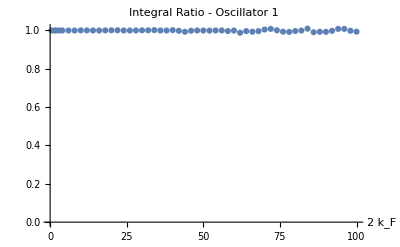

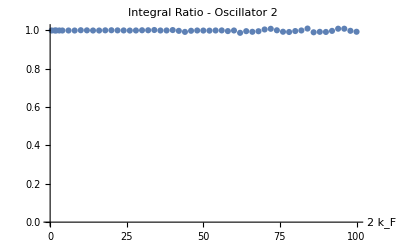

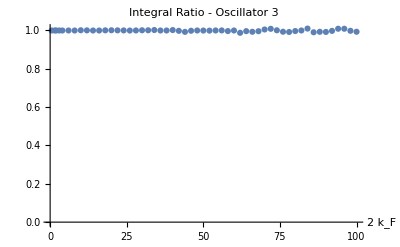

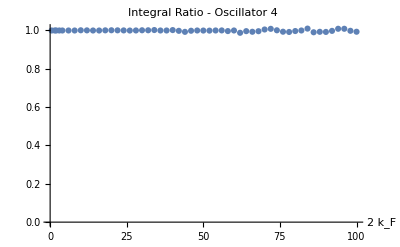

```mathematica
Do[Print[ListPlot[Aratio1to4[[i]],PlotRange->{0,1.01},PlotLabel->StringForm["Integral Ratio - Oscillator ``",ToString[i]],AxesLabel->{"2 k_F"}]],{i,4}]
```

```mathematica
Aratio56 = Table[Join[{{2^-1,Aofq[2^-1,FeTotalparams[[j]]]/("Ai"/.FeTotalparams[[j]])},{1.5,Aofq[1.5,FeTotalparams[[j]]]/("Ai"/.FeTotalparams[[j]])},{3,Aofq[3,FeTotalparams[[j]]]/("Ai"/.FeTotalparams[[j]])}},Table[{2 i,Aofq[2 i,FeTotalparams[[j]]]/("Ai"/.FeTotalparams[[j]])},{i,1,50}]],{j,5,6}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in OpticalFits`Private`u near {OpticalFits`Private`u} = {1.92918}. NIntegrate obtained 0.0543435 and 8.11288×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in OpticalFits`Private`u near {OpticalFits`Private`u} = {3.16426}. NIntegrate obtained 0.00607002 and 2.6047×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in OpticalFits`Private`u near {OpticalFits`Private`u} = {4.40997}. NIntegrate obtained 0.00151745 and 1.53183×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

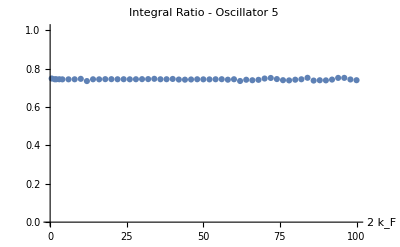

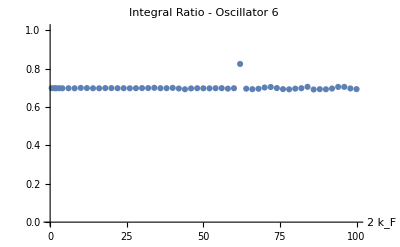

```mathematica
ListPlot[Aratio56[[1]],PlotRange->{0,1.01},PlotLabel->StringForm["Integral Ratio - Oscillator ``",ToString[5]],AxesLabel->{"2 k_F"}]
ListPlot[Aratio56[[2]],PlotRange->{0,1.01},PlotLabel->StringForm["Integral Ratio - Oscillator ``",ToString[6]],AxesLabel->{"2 k_F"}]
```

```mathematica
FeTotalparams[[5]]=RescaleAi[FeTotalparams[[5]],0.75]
FeTotalparams[[6]]=RescaleAi[FeTotalparams[[6]],0.70]
```

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00144809,ωedgei→1.09042×10^18}

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→1.98161×10^-6,ωedgei→1.09893×10^19}

```mathematica
FeTotalparamsExtrapolatedν[[5]]=RescaleAi[FeTotalparamsExtrapolatedν[[5]],0.75]
FeTotalparamsExtrapolatedν[[6]]=RescaleAi[FeTotalparamsExtrapolatedν[[6]],0.70]
```

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.55522×10^17,Ai→0.00144809,ωedgei→1.09042×10^18}

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.23434×10^18,Ai→1.98161×10^-6,ωedgei→1.09893×10^19}

```mathematica
FeTotalparamsExtrapolatedνn[[5]]=RescaleAi[FeTotalparamsExtrapolatedνn[[5]],0.75]
FeTotalparamsExtrapolatedνn[[6]]=RescaleAi[FeTotalparamsExtrapolatedνn[[6]],0.70]
```

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→6.91658×10^32,qF→2.73592×10^11,vF→3.16839×10^7,μ→4.57262×10^-16,ωp→1.48463×10^18,α→1/137,χ→0.148322,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→6053.18,nI→8.64572×10^31,Z→8,M→9.27329×10^-26,EF→4.57262×10^-16,ωi→1.48463×10^18,νi→7.55522×10^17,Ai→0.00144809,ωedgei→1.09042×10^18}

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→6.66733×10^34,qF→1.25446×10^12,vF→1.45275×10^8,μ→9.61328×10^-15,ωp→1.45763×10^19,α→1/137,χ→0.0692675,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→127260.,nI→8.33416×10^33,Z→8,M→9.27329×10^-26,EF→9.61328×10^-15,ωi→1.45763×10^19,νi→5.23434×10^18,Ai→1.98161×10^-6,ωedgei→1.09893×10^19}

#### Run Fe - at crust

```mathematica
(*FeELOutputDict=EnergyLossTableAndInterFITTotalParams[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-2} "c" /.SIConstRepl,<|"mχ"->2,"vχ"->2|>,FeTotalparams,True,"FeELOutputDictSI"]*)
```

```mathematica
FeELOutputDict=EnergyLossTableAndInterFITTotalParams[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-2} "c" /.SIConstRepl,<|"mχ"->6,"vχ"->4|>,FeTotalparams,True,"FeELOutputDictSI"]
```

1 of 24

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.00116074 
Prefactor:	8.19529×10^15
dEdr:	9.5126×10^12

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000940039 
Prefactor:	6.19052×10^15
dEdr:	5.81933×10^12

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000559998 
Prefactor:	1.01998×10^17
dEdr:	5.71185×10^13

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000162759 
Prefactor:	8.78553×10^17
dEdr:	1.42992×10^14

For mχ = 4.45×10^-31 , vχ = 7500.
L:	9.33024×10^-6 
Prefactor:	3.59493×10^18
dEdr:	3.35416×10^13

For mχ = 4.45×10^-31 , vχ = 7500.
L:	5.34975×10^-7 
Prefactor:	2.17433×10^18
dEdr:	1.16321×10^12

dEdr total: 2.50148×10^14

2 of 24

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.0116058 
Prefactor:	8.19529×10^13
dEdr:	9.51128×10^11

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00939926 
Prefactor:	6.19052×10^13
dEdr:	5.81863×10^11

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00559954 
Prefactor:	1.01998×10^15
dEdr:	5.7114×10^12

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00162754 
Prefactor:	8.78553×10^15
dEdr:	1.42988×10^13

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.0000933023 
Prefactor:	3.59493×10^16
dEdr:	3.35416×10^12

For mχ = 4.45×10^-31 , vχ = 75000.
L:	5.34975×10^-6 
Prefactor:	2.17433×10^16
dEdr:	1.16321×10^11

dEdr total: 2.50137×10^13

3 of 24

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.114579 
Prefactor:	8.19529×10^11
dEdr:	9.39006×10^10

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0929053 
Prefactor:	6.19052×10^11
dEdr:	5.75132×10^10

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0555615 
Prefactor:	1.01998×10^13
dEdr:	5.66714×10^11

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0162292 
Prefactor:	8.78553×10^13
dEdr:	1.42582×10^12

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.000932943 
Prefactor:	3.59493×10^14
dEdr:	3.35387×10^11

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0000534978 
Prefactor:	2.17433×10^14
dEdr:	1.16322×10^10

dEdr total: 2.49097×10^12

4 of 24

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	1.20534 
Prefactor:	8.19529×10^9
dEdr:	9.87812×10^9

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.982206 
Prefactor:	6.19052×10^9
dEdr:	6.08037×10^9

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.597842 
Prefactor:	1.01998×10^11
dEdr:	6.09785×10^10

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.151339 
Prefactor:	8.78553×10^11
dEdr:	1.32959×10^11

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.00924909 
Prefactor:	3.59493×10^12
dEdr:	3.32498×10^10

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.000535251 
Prefactor:	2.17433×10^12
dEdr:	1.16381×10^9

dEdr total: 2.4431×10^11

5 of 24

For mχ = 4.45×10^-30 , vχ = 7500.
L:	0.0000662786 
Prefactor:	8.19529×10^15
dEdr:	5.43172×10^11

For mχ = 4.45×10^-30 , vχ = 7500.
L:	0.0000392174 
Prefactor:	6.19052×10^15
dEdr:	2.42776×10^11

For mχ = 4.45×10^-30 , vχ = 7500.
L:	0.0000269417 
Prefactor:	1.01998×10^17
dEdr:	2.74799×10^12

For mχ = 4.45×10^-30 , vχ = 7500.
L:	9.58557×10^-6 
Prefactor:	8.78553×10^17
dEdr:	8.42144×10^12

For mχ = 4.45×10^-30 , vχ = 7500.
L:	4.51478×10^-7 
Prefactor:	3.59493×10^18
dEdr:	1.62303×10^12

For mχ = 4.45×10^-30 , vχ = 7500.
L:	2.2785×10^-8 
Prefactor:	2.17433×10^18
dEdr:	4.9542×10^10

dEdr total: 1.3628×10^13

6 of 24

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.000680666 
Prefactor:	8.19529×10^13
dEdr:	5.57825×10^10

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.000399797 
Prefactor:	6.19052×10^13
dEdr:	2.47495×10^10

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.000272572 
Prefactor:	1.01998×10^15
dEdr:	2.78017×10^11

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.0000962013 
Prefactor:	8.78553×10^15
dEdr:	8.45179×10^11

For mχ = 4.45×10^-30 , vχ = 75000.
L:	4.51571×10^-6 
Prefactor:	3.59493×10^16
dEdr:	1.62337×10^11

For mχ = 4.45×10^-30 , vχ = 75000.
L:	2.27853×10^-7 
Prefactor:	2.17433×10^16
dEdr:	4.95427×10^9

dEdr total: 1.37102×10^12

7 of 24

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.0242272 
Prefactor:	8.19529×10^11
dEdr:	1.98549×10^10

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.0116092 
Prefactor:	6.19052×10^11
dEdr:	7.18668×10^9

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.00587189 
Prefactor:	1.01998×10^13
dEdr:	5.98919×10^10

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.00130646 
Prefactor:	8.78553×10^13
dEdr:	1.14779×10^11

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.0000460829 
Prefactor:	3.59493×10^14
dEdr:	1.65665×10^10

For mχ = 4.45×10^-30 , vχ = 750000.
L:	2.28155×10^-6 
Prefactor:	2.17433×10^14
dEdr:	4.96085×10^8

dEdr total: 2.18775×10^11

8 of 24

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	1.46572 
Prefactor:	8.19529×10^9
dEdr:	1.2012×10^10

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	1.19748 
Prefactor:	6.19052×10^9
dEdr:	7.413×10^9

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.762186 
Prefactor:	1.01998×10^11
dEdr:	7.77412×10^10

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.198633 
Prefactor:	8.78553×10^11
dEdr:	1.74509×10^11

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.00137738 
Prefactor:	3.59493×10^12
dEdr:	4.95157×10^9

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.0000258405 
Prefactor:	2.17433×10^12
dEdr:	5.61858×10^7

dEdr total: 2.76683×10^11

9 of 24

For mχ = 4.45×10^-29 , vχ = 7500.
L:	6.74067×10^-7 
Prefactor:	8.19529×10^15
dEdr:	5.52417×10^9

For mχ = 4.45×10^-29 , vχ = 7500.
L:	3.86345×10^-7 
Prefactor:	6.19052×10^15
dEdr:	2.39168×10^9

For mχ = 4.45×10^-29 , vχ = 7500.
L:	2.68082×10^-7 
Prefactor:	1.01998×10^17
dEdr:	2.73438×10^10

For mχ = 4.45×10^-29 , vχ = 7500.
L:	9.67645×10^-8 
Prefactor:	8.78553×10^17
dEdr:	8.50128×10^10

For mχ = 4.45×10^-29 , vχ = 7500.
L:	4.51879×10^-9 
Prefactor:	3.59493×10^18
dEdr:	1.62447×10^10

For mχ = 4.45×10^-29 , vχ = 7500.
L:	2.26213×10^-10 
Prefactor:	2.17433×10^18
dEdr:	4.91863×10^8

dEdr total: 1.37009×10^11

10 of 24

For mχ = 4.45×10^-29 , vχ = 75000.
L:	0.0000253134 
Prefactor:	8.19529×10^13
dEdr:	2.07451×10^9

For mχ = 4.45×10^-29 , vχ = 75000.
L:	0.0000112281 
Prefactor:	6.19052×10^13
dEdr:	6.9508×10^8

For mχ = 4.45×10^-29 , vχ = 75000.
L:	5.87609×10^-6 
Prefactor:	1.01998×10^15
dEdr:	5.99348×10^9

For mχ = 4.45×10^-29 , vχ = 75000.
L:	1.33953×10^-6 
Prefactor:	8.78553×10^15
dEdr:	1.17685×10^10

For mχ = 4.45×10^-29 , vχ = 75000.
L:	4.61524×10^-8 
Prefactor:	3.59493×10^16
dEdr:	1.65915×10^9

For mχ = 4.45×10^-29 , vχ = 75000.
L:	2.26523×10^-9 
Prefactor:	2.17433×10^16
dEdr:	4.92536×10^7

dEdr total: 2.224×10^10

11 of 24

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.0179296 
Prefactor:	8.19529×10^11
dEdr:	1.46938×10^10

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.00742999 
Prefactor:	6.19052×10^11
dEdr:	4.59955×10^9

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.00320711 
Prefactor:	1.01998×10^13
dEdr:	3.27118×10^10

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.000381819 
Prefactor:	8.78553×10^13
dEdr:	3.35448×10^10

For mχ = 4.45×10^-29 , vχ = 750000.
L:	1.42583×10^-6 
Prefactor:	3.59493×10^14
dEdr:	5.12576×10^8

For mχ = 4.45×10^-29 , vχ = 750000.
L:	2.57489×10^-8 
Prefactor:	2.17433×10^14
dEdr:	5.59867×10^6

dEdr total: 8.60681×10^10

12 of 24

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	1.45653 
Prefactor:	8.19529×10^9
dEdr:	1.19367×10^10

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	1.19001 
Prefactor:	6.19052×10^9
dEdr:	7.36678×10^9

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	0.756514 
Prefactor:	1.01998×10^11
dEdr:	7.71627×10^10

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	0.195231 
Prefactor:	8.78553×10^11
dEdr:	1.71521×10^11

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	0.000962787 
Prefactor:	3.59493×10^12
dEdr:	3.46115×10^9

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	3.35284×10^-6 
Prefactor:	2.17433×10^12
dEdr:	7.29018×10^6

dEdr total: 2.71456×10^11

13 of 24

For mχ = 4.45×10^-28 , vχ = 7500.
L:	2.53368×10^-8 
Prefactor:	8.19529×10^15
dEdr:	2.07642×10^8

For mχ = 4.45×10^-28 , vχ = 7500.
L:	1.12304×10^-8 
Prefactor:	6.19052×10^15
dEdr:	6.95219×10^7

For mχ = 4.45×10^-28 , vχ = 7500.
L:	5.8787×10^-9 
Prefactor:	1.01998×10^17
dEdr:	5.99614×10^8

For mχ = 4.45×10^-28 , vχ = 7500.
L:	1.34016×10^-9 
Prefactor:	8.78553×10^17
dEdr:	1.1774×10^9

For mχ = 4.45×10^-28 , vχ = 7500.
L:	4.61638×10^-11 
Prefactor:	3.59493×10^18
dEdr:	1.65956×10^8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00006}. NIntegrate obtained 2.26569×10^-12 and 3.86375×10^-18 for the integral and error estimates.

For mχ = 4.45×10^-28 , vχ = 7500.
L:	2.26569×10^-12 
Prefactor:	2.17433×10^18
dEdr:	4.92637×10^6

dEdr total: 2.22506×10^9

14 of 24

For mχ = 4.45×10^-28 , vχ = 75000.
L:	0.0000188376 
Prefactor:	8.19529×10^13
dEdr:	1.5438×10^9

For mχ = 4.45×10^-28 , vχ = 75000.
L:	7.47826×10^-6 
Prefactor:	6.19052×10^13
dEdr:	4.62943×10^8

For mχ = 4.45×10^-28 , vχ = 75000.
L:	3.25609×10^-6 
Prefactor:	1.01998×10^15
dEdr:	3.32114×10^9

For mχ = 4.45×10^-28 , vχ = 75000.
L:	3.85727×10^-7 
Prefactor:	8.78553×10^15
dEdr:	3.38882×10^9

For mχ = 4.45×10^-28 , vχ = 75000.
L:	1.42703×10^-9 
Prefactor:	3.59493×10^16
dEdr:	5.13009×10^7

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00006}. NIntegrate obtained 2.57553×10^-11 and 2.73265×10^-17 for the integral and error estimates.

For mχ = 4.45×10^-28 , vχ = 75000.
L:	2.57553×10^-11 
Prefactor:	2.17433×10^16
dEdr:	560006.

dEdr total: 8.76856×10^9

15 of 24

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.0178683 
Prefactor:	8.19529×10^11
dEdr:	1.46436×10^10

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.00738969 
Prefactor:	6.19052×10^11
dEdr:	4.5746×10^9

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.00318128 
Prefactor:	1.01998×10^13
dEdr:	3.24483×10^10

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.000372636 
Prefactor:	8.78553×10^13
dEdr:	3.27381×10^10

For mχ = 4.45×10^-28 , vχ = 750000.
L:	9.79427×10^-7 
Prefactor:	3.59493×10^14
dEdr:	3.52097×10^8

For mχ = 4.45×10^-28 , vχ = 750000.
L:	3.35591×10^-9 
Prefactor:	2.17433×10^14
dEdr:	729686.

dEdr total: 8.47574×10^10

16 of 24

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	1.45644 
Prefactor:	8.19529×10^9
dEdr:	1.19359×10^10

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	1.18994 
Prefactor:	6.19052×10^9
dEdr:	7.36633×10^9

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	0.756458 
Prefactor:	1.01998×10^11
dEdr:	7.7157×10^10

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	0.195198 
Prefactor:	8.78553×10^11
dEdr:	1.71492×10^11

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	0.000958704 
Prefactor:	3.59493×10^12
dEdr:	3.44648×10^9

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	3.13014×10^-6 
Prefactor:	2.17433×10^12
dEdr:	6.80596×10^6

dEdr total: 2.71404×10^11

17 of 24

For mχ = 4.45×10^-27 , vχ = 7500.
L:	1.885×10^-8 
Prefactor:	8.19529×10^15
dEdr:	1.54481×10^8

For mχ = 4.45×10^-27 , vχ = 7500.
L:	7.48007×10^-9 
Prefactor:	6.19052×10^15
dEdr:	4.63055×10^7

For mχ = 4.45×10^-27 , vχ = 7500.
L:	3.25683×10^-9 
Prefactor:	1.01998×10^17
dEdr:	3.3219×10^8

For mχ = 4.45×10^-27 , vχ = 7500.
L:	3.8577×10^-10 
Prefactor:	8.78553×10^17
dEdr:	3.38919×10^8

For mχ = 4.45×10^-27 , vχ = 7500.
L:	1.42705×10^-12 
Prefactor:	3.59493×10^18
dEdr:	5.13013×10^6

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00006}. NIntegrate obtained 2.57554×10^-14 and 2.76681×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-27 , vχ = 7500.
L:	2.57554×10^-14 
Prefactor:	2.17433×10^18
dEdr:	56000.8

dEdr total: 8.77081×10^8

18 of 24

For mχ = 4.45×10^-27 , vχ = 75000.
L:	0.0000187729 
Prefactor:	8.19529×10^13
dEdr:	1.53849×10^9

For mχ = 4.45×10^-27 , vχ = 75000.
L:	7.44077×10^-6 
Prefactor:	6.19052×10^13
dEdr:	4.60622×10^8

For mχ = 4.45×10^-27 , vχ = 75000.
L:	3.22989×10^-6 
Prefactor:	1.01998×10^15
dEdr:	3.29442×10^9

For mχ = 4.45×10^-27 , vχ = 75000.
L:	3.76188×10^-7 
Prefactor:	8.78553×10^15
dEdr:	3.30501×10^9

For mχ = 4.45×10^-27 , vχ = 75000.
L:	9.79675×10^-10 
Prefactor:	3.59493×10^16
dEdr:	3.52186×10^7

For mχ = 4.45×10^-27 , vχ = 75000.
L:	3.35596×10^-12 
Prefactor:	2.17433×10^16
dEdr:	72969.6

dEdr total: 8.63383×10^9

19 of 24

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.0178676 
Prefactor:	8.19529×10^11
dEdr:	1.4643×10^10

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.00738929 
Prefactor:	6.19052×10^11
dEdr:	4.57435×10^9

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.00318102 
Prefactor:	1.01998×10^13
dEdr:	3.24457×10^10

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.000372544 
Prefactor:	8.78553×10^13
dEdr:	3.273×10^10

For mχ = 4.45×10^-27 , vχ = 750000.
L:	9.74962×10^-7 
Prefactor:	3.59493×10^14
dEdr:	3.50492×10^8

For mχ = 4.45×10^-27 , vχ = 750000.
L:	3.13194×10^-9 
Prefactor:	2.17433×10^14
dEdr:	680988.

dEdr total: 8.47443×10^10

20 of 24

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	1.45644 
Prefactor:	8.19529×10^9
dEdr:	1.19359×10^10

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	1.18994 
Prefactor:	6.19052×10^9
dEdr:	7.36633×10^9

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	0.756458 
Prefactor:	1.01998×10^11
dEdr:	7.71569×10^10

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	0.195197 
Prefactor:	8.78553×10^11
dEdr:	1.71491×10^11

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	0.000958663 
Prefactor:	3.59493×10^12
dEdr:	3.44633×10^9

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	3.12791×10^-6 
Prefactor:	2.17433×10^12
dEdr:	6.80112×10^6

dEdr total: 2.71404×10^11

21 of 24

For mχ = 4.45×10^-26 , vχ = 7500.
L:	1.87851×10^-8 
Prefactor:	8.19529×10^15
dEdr:	1.53949×10^8

For mχ = 4.45×10^-26 , vχ = 7500.
L:	7.44257×10^-9 
Prefactor:	6.19052×10^15
dEdr:	4.60733×10^7

For mχ = 4.45×10^-26 , vχ = 7500.
L:	3.23061×10^-9 
Prefactor:	1.01998×10^17
dEdr:	3.29515×10^8

For mχ = 4.45×10^-26 , vχ = 7500.
L:	3.76226×10^-10 
Prefactor:	8.78553×10^17
dEdr:	3.30534×10^8

For mχ = 4.45×10^-26 , vχ = 7500.
L:	9.79677×10^-13 
Prefactor:	3.59493×10^18
dEdr:	3.52187×10^6

For mχ = 4.45×10^-26 , vχ = 7500.
L:	3.35596×10^-15 
Prefactor:	2.17433×10^18
dEdr:	7296.97

dEdr total: 8.63601×10^8

22 of 24

For mχ = 4.45×10^-26 , vχ = 75000.
L:	0.0000187722 
Prefactor:	8.19529×10^13
dEdr:	1.53844×10^9

For mχ = 4.45×10^-26 , vχ = 75000.
L:	7.4404×10^-6 
Prefactor:	6.19052×10^13
dEdr:	4.60599×10^8

For mχ = 4.45×10^-26 , vχ = 75000.
L:	3.22963×10^-6 
Prefactor:	1.01998×10^15
dEdr:	3.29415×10^9

For mχ = 4.45×10^-26 , vχ = 75000.
L:	3.76092×10^-7 
Prefactor:	8.78553×10^15
dEdr:	3.30417×10^9

For mχ = 4.45×10^-26 , vχ = 75000.
L:	9.75201×10^-10 
Prefactor:	3.59493×10^16
dEdr:	3.50578×10^7

For mχ = 4.45×10^-26 , vχ = 75000.
L:	3.13196×10^-12 
Prefactor:	2.17433×10^16
dEdr:	68099.3

dEdr total: 8.63248×10^9

23 of 24

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.0178676 
Prefactor:	8.19529×10^11
dEdr:	1.4643×10^10

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.00738928 
Prefactor:	6.19052×10^11
dEdr:	4.57435×10^9

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.00318102 
Prefactor:	1.01998×10^13
dEdr:	3.24457×10^10

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.000372543 
Prefactor:	8.78553×10^13
dEdr:	3.27299×10^10

For mχ = 4.45×10^-26 , vχ = 750000.
L:	9.74918×10^-7 
Prefactor:	3.59493×10^14
dEdr:	3.50476×10^8

For mχ = 4.45×10^-26 , vχ = 750000.
L:	3.1297×10^-9 
Prefactor:	2.17433×10^14
dEdr:	680501.

dEdr total: 8.47441×10^10

24 of 24

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	1.45644 
Prefactor:	8.19529×10^9
dEdr:	1.19359×10^10

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	1.18994 
Prefactor:	6.19052×10^9
dEdr:	7.36633×10^9

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	0.756458 
Prefactor:	1.01998×10^11
dEdr:	7.71569×10^10

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	0.195197 
Prefactor:	8.78553×10^11
dEdr:	1.71491×10^11

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	0.000958663 
Prefactor:	3.59493×10^12
dEdr:	3.44633×10^9

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	3.12789×10^-6 
Prefactor:	2.17433×10^12
dEdr:	6.80107×10^6

dEdr total: 2.71404×10^11

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-31,4.45×10^-31,4.45×10^-31,4.45×10^-31},{4.45×10^-30,4.45×10^-30,4.45×10^-30,4.45×10^-30},{4.45×10^-29,4.45×10^-29,4.45×10^-29,4.45×10^-29},{4.45×10^-28,4.45×10^-28,4.45×10^-28,4.45×10^-28},{4.45×10^-27,4.45×10^-27,4.45×10^-27,4.45×10^-27},{4.45×10^-26,4.45×10^-26,4.45×10^-26,4.45×10^-26}},vχMesh→{{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6}},EnergyLossMesh→{{2.50148×10^14,2.50137×10^13,2.49097×10^12,2.4431×10^11},{1.3628×10^13,1.37102×10^12,2.18775×10^11,2.76683×10^11},{1.37009×10^11,2.224×10^10,8.60681×10^10,2.71456×10^11},{2.22506×10^9,8.76856×10^9,8.47574×10^10,2.71404×10^11},{8.77081×10^8,8.63383×10^9,8.47443×10^10,2.71404×10^11},{8.63601×10^8,8.63248×10^9,8.47441×10^10,2.71404×10^11}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00144809,ωedgei→1.09042×10^18},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→1.98161×10^-6,ωedgei→1.09893×10^19}},fname→FeELOutputDictSI,kinlist→<|mχ→{4.45×10^-31,4.45×10^-30,4.45×10^-29,4.45×10^-28,4.45×10^-27,4.45×10^-26},vχ→{7500.,75000.,750000.,7.5×10^6}|>,meshdims→<|mχ→6,vχ→4|>,timesMesh→{{34.1233,36.3146,35.078,87.8457},{36.9107,33.7301,37.4681,99.9867},{39.2428,36.711,38.7031,76.6925},{39.3594,36.4325,49.0473,145.351},{121.449,99.3101,38.0587,85.4639},{36.0339,44.816,38.6308,83.0538}},totalTime→1409.81|>

#### Plot Iron - at crust

```mathematica
FeELOutputDictSI=ReadIt[NotebookDirectory[]<>"FeELOutputDictSI"];
```

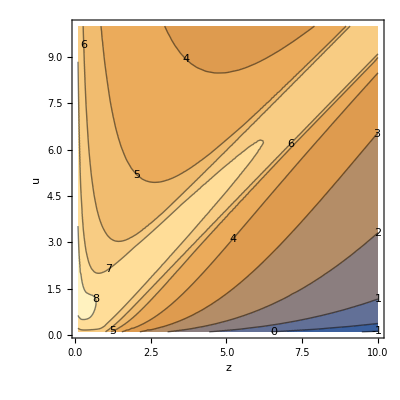

```mathematica
Utilities`ContourTotalParams[FeELOutputDictSI[["fitparams"]]]
```

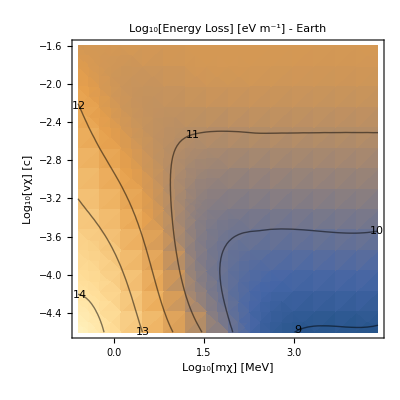

```mathematica
EnergyLoss`PlotEL[FeELOutputDictSI]
```

#### Run Fe - ν rescaled for the core

```mathematica
(*FeELOutputDict=EnergyLossTableAndInterFITTotalParams[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-2} "c" /.SIConstRepl,<|"mχ"->2,"vχ"->2|>,FeTotalparams,True,"FeELOutputDictSI"]*)
```

```mathematica
FeELOutputDictSIExtrapolatedν=EnergyLossTableAndInterFITTotalParams[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-2} "c" /.SIConstRepl,<|"mχ"->6,"vχ"->4|>,FeTotalparamsExtrapolatedν,True,"FeELOutputDictSIExtrapolatedν"]
```

1 of 24

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000994811 
Prefactor:	8.19529×10^15
dEdr:	8.15277×10^12

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000817081 
Prefactor:	6.19052×10^15
dEdr:	5.05816×10^12

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000512713 
Prefactor:	1.01998×10^17
dEdr:	5.22956×10^13

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000158287 
Prefactor:	8.78553×10^17
dEdr:	1.39063×10^14

For mχ = 4.45×10^-31 , vχ = 7500.
L:	9.31827×10^-6 
Prefactor:	3.59493×10^18
dEdr:	3.34985×10^13

For mχ = 4.45×10^-31 , vχ = 7500.
L:	5.34951×10^-7 
Prefactor:	2.17433×10^18
dEdr:	1.16316×10^12

dEdr total: 2.39231×10^14

2 of 24

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00994709 
Prefactor:	8.19529×10^13
dEdr:	8.15193×10^11

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00816993 
Prefactor:	6.19052×10^13
dEdr:	5.05761×10^11

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00512674 
Prefactor:	1.01998×10^15
dEdr:	5.22916×10^12

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00158282 
Prefactor:	8.78553×10^15
dEdr:	1.39059×10^13

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.0000931826 
Prefactor:	3.59493×10^16
dEdr:	3.34985×10^12

For mχ = 4.45×10^-31 , vχ = 75000.
L:	5.34951×10^-6 
Prefactor:	2.17433×10^16
dEdr:	1.16316×10^11

dEdr total: 2.39222×10^13

3 of 24

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0985476 
Prefactor:	8.19529×10^11
dEdr:	8.07625×10^10

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0808689 
Prefactor:	6.19052×10^11
dEdr:	5.00621×10^10

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0508923 
Prefactor:	1.01998×10^13
dEdr:	5.1909×10^11

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0157832 
Prefactor:	8.78553×10^13
dEdr:	1.38664×10^12

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.000931744 
Prefactor:	3.59493×10^14
dEdr:	3.34956×10^11

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0000534954 
Prefactor:	2.17433×10^14
dEdr:	1.16317×10^10

dEdr total: 2.38314×10^12

4 of 24

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	1.0663 
Prefactor:	8.19529×10^9
dEdr:	8.73866×10^9

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.869994 
Prefactor:	6.19052×10^9
dEdr:	5.38571×10^9

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.54813 
Prefactor:	1.01998×10^11
dEdr:	5.5908×10^10

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.148458 
Prefactor:	8.78553×10^11
dEdr:	1.30429×10^11

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.00923603 
Prefactor:	3.59493×10^12
dEdr:	3.32029×10^10

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.000535227 
Prefactor:	2.17433×10^12
dEdr:	1.16376×10^9

dEdr total: 2.34828×10^11

5 of 24

For mχ = 4.45×10^-30 , vχ = 7500.
L:	0.0000834417 
Prefactor:	8.19529×10^15
dEdr:	6.83828×10^11

For mχ = 4.45×10^-30 , vχ = 7500.
L:	0.0000476199 
Prefactor:	6.19052×10^15
dEdr:	2.94792×10^11

For mχ = 4.45×10^-30 , vχ = 7500.
L:	0.0000301534 
Prefactor:	1.01998×10^17
dEdr:	3.07557×10^12

For mχ = 4.45×10^-30 , vχ = 7500.
L:	9.88494×10^-6 
Prefactor:	8.78553×10^17
dEdr:	8.68445×10^12

For mχ = 4.45×10^-30 , vχ = 7500.
L:	4.52159×10^-7 
Prefactor:	3.59493×10^18
dEdr:	1.62548×10^12

For mχ = 4.45×10^-30 , vχ = 7500.
L:	2.27868×10^-8 
Prefactor:	2.17433×10^18
dEdr:	4.9546×10^10

dEdr total: 1.44137×10^13

6 of 24

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.000855663 
Prefactor:	8.19529×10^13
dEdr:	7.0124×10^10

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.000485136 
Prefactor:	6.19052×10^13
dEdr:	3.00324×10^10

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.000305025 
Prefactor:	1.01998×10^15
dEdr:	3.11119×10^11

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.0000992067 
Prefactor:	8.78553×10^15
dEdr:	8.71583×10^11

For mχ = 4.45×10^-30 , vχ = 75000.
L:	4.52251×10^-6 
Prefactor:	3.59493×10^16
dEdr:	1.62581×10^11

For mχ = 4.45×10^-30 , vχ = 75000.
L:	2.27871×10^-7 
Prefactor:	2.17433×10^16
dEdr:	4.95467×10^9

dEdr total: 1.45039×10^12

7 of 24

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.0278074 
Prefactor:	8.19529×10^11
dEdr:	2.2789×10^10

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.0136269 
Prefactor:	6.19052×10^11
dEdr:	8.43573×10^9

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.00650525 
Prefactor:	1.01998×10^13
dEdr:	6.6352×10^10

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.00134782 
Prefactor:	8.78553×10^13
dEdr:	1.18413×10^11

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.0000461536 
Prefactor:	3.59493×10^14
dEdr:	1.65919×10^10

For mχ = 4.45×10^-30 , vχ = 750000.
L:	2.28174×10^-6 
Prefactor:	2.17433×10^14
dEdr:	4.96125×10^8

dEdr total: 2.33078×10^11

8 of 24

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	1.32118 
Prefactor:	8.19529×10^9
dEdr:	1.08274×10^10

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	1.08144 
Prefactor:	6.19052×10^9
dEdr:	6.6947×10^9

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.706204 
Prefactor:	1.01998×10^11
dEdr:	7.20312×10^10

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.192263 
Prefactor:	8.78553×10^11
dEdr:	1.68913×10^11

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.00138043 
Prefactor:	3.59493×10^12
dEdr:	4.96255×10^9

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.000025843 
Prefactor:	2.17433×10^12
dEdr:	5.61913×10^7

dEdr total: 2.63485×10^11

9 of 24

For mχ = 4.45×10^-29 , vχ = 7500.
L:	8.72788×10^-7 
Prefactor:	8.19529×10^15
dEdr:	7.15275×10^9

For mχ = 4.45×10^-29 , vχ = 7500.
L:	4.82357×10^-7 
Prefactor:	6.19052×10^15
dEdr:	2.98604×10^9

For mχ = 4.45×10^-29 , vχ = 7500.
L:	3.04516×10^-7 
Prefactor:	1.01998×10^17
dEdr:	3.10599×10^10

For mχ = 4.45×10^-29 , vχ = 7500.
L:	1.00159×10^-7 
Prefactor:	8.78553×10^17
dEdr:	8.79953×10^10

For mχ = 4.45×10^-29 , vχ = 7500.
L:	4.52697×10^-9 
Prefactor:	3.59493×10^18
dEdr:	1.62742×10^10

For mχ = 4.45×10^-29 , vχ = 7500.
L:	2.26236×10^-10 
Prefactor:	2.17433×10^18
dEdr:	4.91913×10^8

dEdr total: 1.4596×10^11

10 of 24

For mχ = 4.45×10^-29 , vχ = 75000.
L:	0.0000335339 
Prefactor:	8.19529×10^13
dEdr:	2.7482×10^9

For mχ = 4.45×10^-29 , vχ = 75000.
L:	0.0000142237 
Prefactor:	6.19052×10^13
dEdr:	8.80519×10^8

For mχ = 4.45×10^-29 , vχ = 75000.
L:	6.75643×10^-6 
Prefactor:	1.01998×10^15
dEdr:	6.8914×10^9

For mχ = 4.45×10^-29 , vχ = 75000.
L:	1.39123×10^-6 
Prefactor:	8.78553×10^15
dEdr:	1.22227×10^10

For mχ = 4.45×10^-29 , vχ = 75000.
L:	4.62374×10^-8 
Prefactor:	3.59493×10^16
dEdr:	1.6622×10^9

For mχ = 4.45×10^-29 , vχ = 75000.
L:	2.26546×10^-9 
Prefactor:	2.17433×10^16
dEdr:	4.92586×10^7

dEdr total: 2.44542×10^10

11 of 24

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.0216803 
Prefactor:	8.19529×10^11
dEdr:	1.77677×10^10

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.00916827 
Prefactor:	6.19052×10^11
dEdr:	5.67563×10^9

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.00367565 
Prefactor:	1.01998×10^13
dEdr:	3.74908×10^10

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.000399326 
Prefactor:	8.78553×10^13
dEdr:	3.50829×10^10

For mχ = 4.45×10^-29 , vχ = 750000.
L:	1.42982×10^-6 
Prefactor:	3.59493×10^14
dEdr:	5.14012×10^8

For mχ = 4.45×10^-29 , vχ = 750000.
L:	2.5752×10^-8 
Prefactor:	2.17433×10^14
dEdr:	5.59934×10^6

dEdr total: 9.65366×10^10

12 of 24

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	1.31193 
Prefactor:	8.19529×10^9
dEdr:	1.07516×10^10

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	1.07394 
Prefactor:	6.19052×10^9
dEdr:	6.64826×10^9

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	0.700468 
Prefactor:	1.01998×10^11
dEdr:	7.14461×10^10

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	0.188806 
Prefactor:	8.78553×10^11
dEdr:	1.65876×10^11

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	0.000965625 
Prefactor:	3.59493×10^12
dEdr:	3.47136×10^9

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	3.35365×10^-6 
Prefactor:	2.17433×10^12
dEdr:	7.29196×10^6

dEdr total: 2.582×10^11

13 of 24

For mχ = 4.45×10^-28 , vχ = 7500.
L:	3.36223×10^-8 
Prefactor:	8.19529×10^15
dEdr:	2.75545×10^8

For mχ = 4.45×10^-28 , vχ = 7500.
L:	1.42358×10^-8 
Prefactor:	6.19052×10^15
dEdr:	8.81271×10^7

For mχ = 4.45×10^-28 , vχ = 7500.
L:	6.76134×10^-9 
Prefactor:	1.01998×10^17
dEdr:	6.89641×10^8

For mχ = 4.45×10^-28 , vχ = 7500.
L:	1.39194×10^-9 
Prefactor:	8.78553×10^17
dEdr:	1.2229×10^9

For mχ = 4.45×10^-28 , vχ = 7500.
L:	4.62488×10^-11 
Prefactor:	3.59493×10^18
dEdr:	1.66261×10^8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00006}. NIntegrate obtained 2.26593×10^-12 and 3.85729×10^-18 for the integral and error estimates.

For mχ = 4.45×10^-28 , vχ = 7500.
L:	2.26593×10^-12 
Prefactor:	2.17433×10^18
dEdr:	4.92687×10^6

dEdr total: 2.4474×10^9

14 of 24

For mχ = 4.45×10^-28 , vχ = 75000.
L:	0.0000251849 
Prefactor:	8.19529×10^13
dEdr:	2.06397×10^9

For mχ = 4.45×10^-28 , vχ = 75000.
L:	9.54984×10^-6 
Prefactor:	6.19052×10^13
dEdr:	5.91184×10^8

For mχ = 4.45×10^-28 , vχ = 75000.
L:	3.78241×10^-6 
Prefactor:	1.01998×10^15
dEdr:	3.85797×10^9

For mχ = 4.45×10^-28 , vχ = 75000.
L:	4.04044×10^-7 
Prefactor:	8.78553×10^15
dEdr:	3.54974×10^9

For mχ = 4.45×10^-28 , vχ = 75000.
L:	1.43104×10^-9 
Prefactor:	3.59493×10^16
dEdr:	5.14449×10^7

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00006}. NIntegrate obtained 2.57584×10^-11 and 2.72559×10^-17 for the integral and error estimates.

For mχ = 4.45×10^-28 , vχ = 75000.
L:	2.57584×10^-11 
Prefactor:	2.17433×10^16
dEdr:	560074.

dEdr total: 1.01149×10^10

15 of 24

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.0216203 
Prefactor:	8.19529×10^11
dEdr:	1.77184×10^10

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.0091248 
Prefactor:	6.19052×10^11
dEdr:	5.64872×10^9

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.00364796 
Prefactor:	1.01998×10^13
dEdr:	3.72084×10^10

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.000389869 
Prefactor:	8.78553×10^13
dEdr:	3.42521×10^10

For mχ = 4.45×10^-28 , vχ = 750000.
L:	9.82619×10^-7 
Prefactor:	3.59493×10^14
dEdr:	3.53245×10^8

For mχ = 4.45×10^-28 , vχ = 750000.
L:	3.35673×10^-9 
Prefactor:	2.17433×10^14
dEdr:	729865.

dEdr total: 9.51815×10^10

16 of 24

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	1.31184 
Prefactor:	8.19529×10^9
dEdr:	1.07509×10^10

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	1.07387 
Prefactor:	6.19052×10^9
dEdr:	6.6478×10^9

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	0.700411 
Prefactor:	1.01998×10^11
dEdr:	7.14404×10^10

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	0.188772 
Prefactor:	8.78553×10^11
dEdr:	1.65846×10^11

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	0.00096154 
Prefactor:	3.59493×10^12
dEdr:	3.45667×10^9

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	3.13094×10^-6 
Prefactor:	2.17433×10^12
dEdr:	6.80769×10^6

dEdr total: 2.58148×10^11

17 of 24

For mχ = 4.45×10^-27 , vχ = 7500.
L:	2.5229×10^-8 
Prefactor:	8.19529×10^15
dEdr:	2.06759×10^8

For mχ = 4.45×10^-27 , vχ = 7500.
L:	9.5547×10^-9 
Prefactor:	6.19052×10^15
dEdr:	5.91485×10^7

For mχ = 4.45×10^-27 , vχ = 7500.
L:	3.78369×10^-9 
Prefactor:	1.01998×10^17
dEdr:	3.85927×10^8

For mχ = 4.45×10^-27 , vχ = 7500.
L:	4.04095×10^-10 
Prefactor:	8.78553×10^17
dEdr:	3.55019×10^8

For mχ = 4.45×10^-27 , vχ = 7500.
L:	1.43105×10^-12 
Prefactor:	3.59493×10^18
dEdr:	5.14453×10^6

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00006}. NIntegrate obtained 2.57585×10^-14 and 2.77077×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-27 , vχ = 7500.
L:	2.57585×10^-14 
Prefactor:	2.17433×10^18
dEdr:	56007.5

dEdr total: 1.01205×10^9

18 of 24

For mχ = 4.45×10^-27 , vχ = 75000.
L:	0.0000251014 
Prefactor:	8.19529×10^13
dEdr:	2.05713×10^9

For mχ = 4.45×10^-27 , vχ = 75000.
L:	9.5031×10^-6 
Prefactor:	6.19052×10^13
dEdr:	5.88291×10^8

For mχ = 4.45×10^-27 , vχ = 75000.
L:	3.75267×10^-6 
Prefactor:	1.01998×10^15
dEdr:	3.82764×10^9

For mχ = 4.45×10^-27 , vχ = 75000.
L:	3.94171×10^-7 
Prefactor:	8.78553×10^15
dEdr:	3.463×10^9

For mχ = 4.45×10^-27 , vχ = 75000.
L:	9.8287×10^-10 
Prefactor:	3.59493×10^16
dEdr:	3.53335×10^7

For mχ = 4.45×10^-27 , vχ = 75000.
L:	3.35678×10^-12 
Prefactor:	2.17433×10^16
dEdr:	72987.5

dEdr total: 9.97146×10^9

19 of 24

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.0216197 
Prefactor:	8.19529×10^11
dEdr:	1.77179×10^10

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.00912436 
Prefactor:	6.19052×10^11
dEdr:	5.64845×10^9

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.00364768 
Prefactor:	1.01998×10^13
dEdr:	3.72055×10^10

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.000389774 
Prefactor:	8.78553×10^13
dEdr:	3.42437×10^10

For mχ = 4.45×10^-27 , vχ = 750000.
L:	9.78146×10^-7 
Prefactor:	3.59493×10^14
dEdr:	3.51637×10^8

For mχ = 4.45×10^-27 , vχ = 750000.
L:	3.13274×10^-9 
Prefactor:	2.17433×10^14
dEdr:	681161.

dEdr total: 9.5168×10^10

20 of 24

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	1.31184 
Prefactor:	8.19529×10^9
dEdr:	1.07509×10^10

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	1.07387 
Prefactor:	6.19052×10^9
dEdr:	6.6478×10^9

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	0.700411 
Prefactor:	1.01998×10^11
dEdr:	7.14403×10^10

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	0.188771 
Prefactor:	8.78553×10^11
dEdr:	1.65846×10^11

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	0.000961499 
Prefactor:	3.59493×10^12
dEdr:	3.45652×10^9

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	3.12871×10^-6 
Prefactor:	2.17433×10^12
dEdr:	6.80285×10^6

dEdr total: 2.58148×10^11

21 of 24

For mχ = 4.45×10^-26 , vχ = 7500.
L:	2.51451×10^-8 
Prefactor:	8.19529×10^15
dEdr:	2.06071×10^8

For mχ = 4.45×10^-26 , vχ = 7500.
L:	9.50789×10^-9 
Prefactor:	6.19052×10^15
dEdr:	5.88588×10^7

For mχ = 4.45×10^-26 , vχ = 7500.
L:	3.75391×10^-9 
Prefactor:	1.01998×10^17
dEdr:	3.8289×10^8

For mχ = 4.45×10^-26 , vχ = 7500.
L:	3.94216×10^-10 
Prefactor:	8.78553×10^17
dEdr:	3.4634×10^8

For mχ = 4.45×10^-26 , vχ = 7500.
L:	9.82872×10^-13 
Prefactor:	3.59493×10^18
dEdr:	3.53336×10^6

For mχ = 4.45×10^-26 , vχ = 7500.
L:	3.35678×10^-15 
Prefactor:	2.17433×10^18
dEdr:	7298.75

dEdr total: 9.97701×10^8

22 of 24

For mχ = 4.45×10^-26 , vχ = 75000.
L:	0.0000251005 
Prefactor:	8.19529×10^13
dEdr:	2.05706×10^9

For mχ = 4.45×10^-26 , vχ = 75000.
L:	9.50263×10^-6 
Prefactor:	6.19052×10^13
dEdr:	5.88262×10^8

For mχ = 4.45×10^-26 , vχ = 75000.
L:	3.75237×10^-6 
Prefactor:	1.01998×10^15
dEdr:	3.82733×10^9

For mχ = 4.45×10^-26 , vχ = 75000.
L:	3.94072×10^-7 
Prefactor:	8.78553×10^15
dEdr:	3.46213×10^9

For mχ = 4.45×10^-26 , vχ = 75000.
L:	9.78388×10^-10 
Prefactor:	3.59493×10^16
dEdr:	3.51724×10^7

For mχ = 4.45×10^-26 , vχ = 75000.
L:	3.13276×10^-12 
Prefactor:	2.17433×10^16
dEdr:	68116.6

dEdr total: 9.97003×10^9

23 of 24

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.0216196 
Prefactor:	8.19529×10^11
dEdr:	1.77179×10^10

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.00912436 
Prefactor:	6.19052×10^11
dEdr:	5.64845×10^9

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.00364768 
Prefactor:	1.01998×10^13
dEdr:	3.72055×10^10

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.000389773 
Prefactor:	8.78553×10^13
dEdr:	3.42437×10^10

For mχ = 4.45×10^-26 , vχ = 750000.
L:	9.78102×10^-7 
Prefactor:	3.59493×10^14
dEdr:	3.51621×10^8

For mχ = 4.45×10^-26 , vχ = 750000.
L:	3.1305×10^-9 
Prefactor:	2.17433×10^14
dEdr:	680674.

dEdr total: 9.51678×10^10

24 of 24

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	1.31184 
Prefactor:	8.19529×10^9
dEdr:	1.07509×10^10

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	1.07387 
Prefactor:	6.19052×10^9
dEdr:	6.6478×10^9

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	0.700411 
Prefactor:	1.01998×10^11
dEdr:	7.14403×10^10

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	0.188771 
Prefactor:	8.78553×10^11
dEdr:	1.65846×10^11

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	0.000961499 
Prefactor:	3.59493×10^12
dEdr:	3.45652×10^9

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	3.12869×10^-6 
Prefactor:	2.17433×10^12
dEdr:	6.8028×10^6

dEdr total: 2.58148×10^11

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-31,4.45×10^-31,4.45×10^-31,4.45×10^-31},{4.45×10^-30,4.45×10^-30,4.45×10^-30,4.45×10^-30},{4.45×10^-29,4.45×10^-29,4.45×10^-29,4.45×10^-29},{4.45×10^-28,4.45×10^-28,4.45×10^-28,4.45×10^-28},{4.45×10^-27,4.45×10^-27,4.45×10^-27,4.45×10^-27},{4.45×10^-26,4.45×10^-26,4.45×10^-26,4.45×10^-26}},vχMesh→{{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6}},EnergyLossMesh→{{2.39231×10^14,2.39222×10^13,2.38314×10^12,2.34828×10^11},{1.44137×10^13,1.45039×10^12,2.33078×10^11,2.63485×10^11},{1.4596×10^11,2.44542×10^10,9.65366×10^10,2.582×10^11},{2.4474×10^9,1.01149×10^10,9.51815×10^10,2.58148×10^11},{1.01205×10^9,9.97146×10^9,9.5168×10^10,2.58148×10^11},{9.97701×10^8,9.97003×10^9,9.51678×10^10,2.58148×10^11}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→3.22338×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→2.37219×10^16,Ai→0.0699144,ωedgei→6.5887×10^12},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→3.49108×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→1.07806×10^17,Ai→0.234383,ωedgei→1.51848×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.55522×10^17,Ai→0.00144809,ωedgei→1.09042×10^18},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.23434×10^18,Ai→1.98161×10^-6,ωedgei→1.09893×10^19}},fname→FeELOutputDictSIExtrapolatedν,kinlist→<|mχ→{4.45×10^-31,4.45×10^-30,4.45×10^-29,4.45×10^-28,4.45×10^-27,4.45×10^-26},vχ→{7500.,75000.,750000.,7.5×10^6}|>,meshdims→<|mχ→6,vχ→4|>,timesMesh→{{30.1503,34.9586,34.3105,73.0446},{29.079,31.0345,32.3763,77.7508},{48.9821,84.7536,101.901,177.743},{100.103,98.8504,97.4022,174.916},{103.844,99.571,91.2918,175.768},{95.5082,90.4147,89.6094,176.382}},totalTime→2149.74|>

#### Plot Iron - ν rescaled for the core

```mathematica
FeELOutputDictSIExtrapolatedν=ReadIt[NotebookDirectory[]<>"FeELOutputDictSIExtrapolatedν"];
```

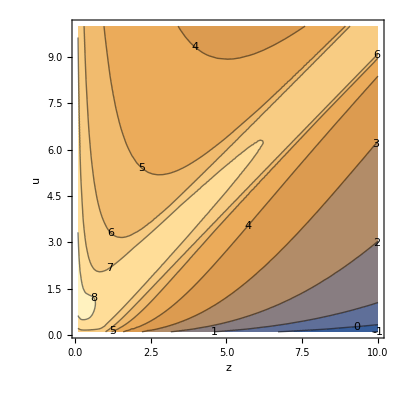

```mathematica
Utilities`ContourTotalParams[FeELOutputDictSIExtrapolatedν[["fitparams"]]]
```

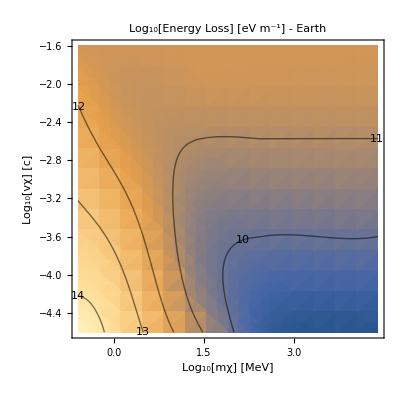

```mathematica
EnergyLoss`PlotEL[FeELOutputDictSIExtrapolatedν]
```

#### Run Fe - ν and n rescaled for the core

```mathematica
(*FeELOutputDict=EnergyLossTableAndInterFITTotalParams[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-2} "c" /.SIConstRepl,<|"mχ"->2,"vχ"->2|>,FeTotalparams,True,"FeELOutputDictSI"]*)
```

```mathematica
FeELOutputDictSIExtrapolatedνn=EnergyLossTableAndInterFITTotalParams[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-2} "c" /.SIConstRepl,<|"mχ"->6,"vχ"->4|>,FeTotalparamsExtrapolatedνn,True,"FeELOutputDictSIExtrapolatedνn"]
```

1 of 24

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000796619 
Prefactor:	1.61943×10^16
dEdr:	1.29007×10^13

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000639016 
Prefactor:	1.22328×10^16
dEdr:	7.81695×10^12

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000399664 
Prefactor:	2.01553×10^17
dEdr:	8.05533×10^13

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.00012307 
Prefactor:	1.73607×10^18
dEdr:	2.13658×10^14

For mχ = 4.45×10^-31 , vχ = 7500.
L:	6.89943×10^-6 
Prefactor:	7.10377×10^18
dEdr:	4.9012×10^13

For mχ = 4.45×10^-31 , vχ = 7500.
L:	3.86366×10^-7 
Prefactor:	4.29659×10^18
dEdr:	1.66006×10^12

dEdr total: 3.65601×10^14

2 of 24

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00796542 
Prefactor:	1.61943×10^14
dEdr:	1.28995×10^12

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00638958 
Prefactor:	1.22328×10^14
dEdr:	7.81623×10^11

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00399639 
Prefactor:	2.01553×10^15
dEdr:	8.05483×10^12

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00123068 
Prefactor:	1.73607×10^16
dEdr:	2.13654×10^13

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.0000689943 
Prefactor:	7.10377×10^16
dEdr:	4.9012×10^12

For mχ = 4.45×10^-31 , vχ = 75000.
L:	3.86366×10^-6 
Prefactor:	4.29659×10^16
dEdr:	1.66006×10^11

dEdr total: 3.6559×10^13

3 of 24

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0789355 
Prefactor:	1.61943×10^12
dEdr:	1.27831×10^11

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0633347 
Prefactor:	1.22328×10^12
dEdr:	7.7476×10^10

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0397242 
Prefactor:	2.01553×10^13
dEdr:	8.00652×10^11

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0122806 
Prefactor:	1.73607×10^14
dEdr:	2.13199×10^12

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.000689913 
Prefactor:	7.10377×10^14
dEdr:	4.90098×10^11

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0000386368 
Prefactor:	4.29659×10^14
dEdr:	1.66007×10^10

dEdr total: 3.64465×10^12

4 of 24

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.856771 
Prefactor:	1.61943×10^10
dEdr:	1.38748×10^10

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.682968 
Prefactor:	1.22328×10^10
dEdr:	8.35461×10^9

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.418502 
Prefactor:	2.01553×10^11
dEdr:	8.43501×10^10

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.111994 
Prefactor:	1.73607×10^12
dEdr:	1.94429×10^11

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.00686899 
Prefactor:	7.10377×10^12
dEdr:	4.87958×10^10

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.000386547 
Prefactor:	4.29659×10^12
dEdr:	1.66083×10^9

dEdr total: 3.51465×10^11

5 of 24

For mχ = 4.45×10^-30 , vχ = 7500.
L:	0.0000565886 
Prefactor:	1.61943×10^16
dEdr:	9.16413×10^11

For mχ = 4.45×10^-30 , vχ = 7500.
L:	0.0000338161 
Prefactor:	1.22328×10^16
dEdr:	4.13665×10^11

For mχ = 4.45×10^-30 , vχ = 7500.
L:	0.0000214177 
Prefactor:	2.01553×10^17
dEdr:	4.3168×10^12

For mχ = 4.45×10^-30 , vχ = 7500.
L:	6.94208×10^-6 
Prefactor:	1.73607×10^18
dEdr:	1.20519×10^13

For mχ = 4.45×10^-30 , vχ = 7500.
L:	3.20621×10^-7 
Prefactor:	7.10377×10^18
dEdr:	2.27762×10^12

For mχ = 4.45×10^-30 , vχ = 7500.
L:	1.61793×10^-8 
Prefactor:	4.29659×10^18
dEdr:	6.95157×10^10

dEdr total: 2.00459×10^13

6 of 24

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.000576938 
Prefactor:	1.61943×10^14
dEdr:	9.34311×10^10

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.000342887 
Prefactor:	1.22328×10^14
dEdr:	4.19446×10^10

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.000216018 
Prefactor:	2.01553×10^15
dEdr:	4.3539×10^11

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.0000696061 
Prefactor:	1.73607×10^16
dEdr:	1.20841×10^12

For mχ = 4.45×10^-30 , vχ = 75000.
L:	3.20669×10^-6 
Prefactor:	7.10377×10^16
dEdr:	2.27796×10^11

For mχ = 4.45×10^-30 , vχ = 75000.
L:	1.61794×10^-7 
Prefactor:	4.29659×10^16
dEdr:	6.95164×10^9

dEdr total: 2.01392×10^12

7 of 24

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.0163337 
Prefactor:	1.61943×10^12
dEdr:	2.64513×10^10

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.0081225 
Prefactor:	1.22328×10^12
dEdr:	9.93607×10^9

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.00399338 
Prefactor:	2.01553×10^13
dEdr:	8.04876×10^10

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.000880969 
Prefactor:	1.73607×10^14
dEdr:	1.52942×10^11

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.0000325468 
Prefactor:	7.10377×10^14
dEdr:	2.31205×10^10

For mχ = 4.45×10^-30 , vχ = 750000.
L:	1.6195×10^-6 
Prefactor:	4.29659×10^14
dEdr:	6.95835×10^8

dEdr total: 2.93633×10^11

8 of 24

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	1.07195 
Prefactor:	1.61943×10^10
dEdr:	1.73595×10^10

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.862351 
Prefactor:	1.22328×10^10
dEdr:	1.0549×10^10

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.553606 
Prefactor:	2.01553×10^11
dEdr:	1.11581×10^11

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.133132 
Prefactor:	1.73607×10^12
dEdr:	2.31125×10^11

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.000802622 
Prefactor:	7.10377×10^12
dEdr:	5.70164×10^9

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.0000177557 
Prefactor:	4.29659×10^12
dEdr:	7.62888×10^7

dEdr total: 3.76392×10^11

9 of 24

For mχ = 4.45×10^-29 , vχ = 7500.
L:	5.81306×10^-7 
Prefactor:	1.61943×10^16
dEdr:	9.41385×10^9

For mχ = 4.45×10^-29 , vχ = 7500.
L:	3.394×10^-7 
Prefactor:	1.22328×10^16
dEdr:	4.15181×10^9

For mχ = 4.45×10^-29 , vχ = 7500.
L:	2.14734×10^-7 
Prefactor:	2.01553×10^17
dEdr:	4.32802×10^10

For mχ = 4.45×10^-29 , vχ = 7500.
L:	6.99177×10^-8 
Prefactor:	1.73607×10^18
dEdr:	1.21382×10^11

For mχ = 4.45×10^-29 , vχ = 7500.
L:	3.19695×10^-9 
Prefactor:	7.10377×10^18
dEdr:	2.27104×10^10

For mχ = 4.45×10^-29 , vχ = 7500.
L:	1.60308×10^-10 
Prefactor:	4.29659×10^18
dEdr:	6.88777×10^8

dEdr total: 2.01627×10^11

10 of 24

For mχ = 4.45×10^-29 , vχ = 75000.
L:	0.0000180464 
Prefactor:	1.61943×10^14
dEdr:	2.92249×10^9

For mχ = 4.45×10^-29 , vχ = 75000.
L:	8.27885×10^-6 
Prefactor:	1.22328×10^14
dEdr:	1.01273×10^9

For mχ = 4.45×10^-29 , vχ = 75000.
L:	4.07009×10^-6 
Prefactor:	2.01553×10^15
dEdr:	8.20338×10^9

For mχ = 4.45×10^-29 , vχ = 75000.
L:	8.96986×10^-7 
Prefactor:	1.73607×10^16
dEdr:	1.55723×10^10

For mχ = 4.45×10^-29 , vχ = 75000.
L:	3.2466×10^-8 
Prefactor:	7.10377×10^16
dEdr:	2.30631×10^9

For mχ = 4.45×10^-29 , vχ = 75000.
L:	1.60467×10^-9 
Prefactor:	4.29659×10^16
dEdr:	6.89462×10^7

dEdr total: 3.00861×10^10

11 of 24

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.0115247 
Prefactor:	1.61943×10^12
dEdr:	1.86635×10^10

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.0048526 
Prefactor:	1.22328×10^12
dEdr:	5.93609×10^9

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.00193153 
Prefactor:	2.01553×10^13
dEdr:	3.89304×10^10

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.000205572 
Prefactor:	1.73607×10^14
dEdr:	3.56886×10^10

For mχ = 4.45×10^-29 , vχ = 750000.
L:	8.21144×10^-7 
Prefactor:	7.10377×10^14
dEdr:	5.83322×10^8

For mχ = 4.45×10^-29 , vχ = 750000.
L:	1.76406×10^-8 
Prefactor:	4.29659×10^14
dEdr:	7.57944×10^6

dEdr total: 9.98096×10^10

12 of 24

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	1.06415 
Prefactor:	1.61943×10^10
dEdr:	1.72332×10^10

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	0.856037 
Prefactor:	1.22328×10^10
dEdr:	1.04717×10^10

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	0.548782 
Prefactor:	2.01553×10^11
dEdr:	1.10609×10^11

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	0.130122 
Prefactor:	1.73607×10^12
dEdr:	2.259×10^11

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	0.000500052 
Prefactor:	7.10377×10^12
dEdr:	3.55225×10^9

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	1.76992×10^-6 
Prefactor:	4.29659×10^12
dEdr:	7.60462×10^6

dEdr total: 3.67774×10^11

13 of 24

For mχ = 4.45×10^-28 , vχ = 7500.
L:	1.80726×10^-8 
Prefactor:	1.61943×10^16
dEdr:	2.92674×10^8

For mχ = 4.45×10^-28 , vχ = 7500.
L:	8.28383×10^-9 
Prefactor:	1.22328×10^16
dEdr:	1.01334×10^8

For mχ = 4.45×10^-28 , vχ = 7500.
L:	4.07227×10^-9 
Prefactor:	2.01553×10^17
dEdr:	8.20777×10^8

For mχ = 4.45×10^-28 , vχ = 7500.
L:	8.97339×10^-10 
Prefactor:	1.73607×10^18
dEdr:	1.55784×10^9

For mχ = 4.45×10^-28 , vχ = 7500.
L:	3.24736×10^-11 
Prefactor:	7.10377×10^18
dEdr:	2.30685×10^8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00006}. NIntegrate obtained 1.60495×10^-12 and 2.52931×10^-18 for the integral and error estimates.

For mχ = 4.45×10^-28 , vχ = 7500.
L:	1.60495×10^-12 
Prefactor:	4.29659×10^18
dEdr:	6.89582×10^6

dEdr total: 3.01021×10^9

14 of 24

For mχ = 4.45×10^-28 , vχ = 75000.
L:	0.000012429 
Prefactor:	1.61943×10^14
dEdr:	2.0128×10^9

For mχ = 4.45×10^-28 , vχ = 75000.
L:	4.9712×10^-6 
Prefactor:	1.22328×10^14
dEdr:	6.08116×10^8

For mχ = 4.45×10^-28 , vχ = 75000.
L:	1.96518×10^-6 
Prefactor:	2.01553×10^15
dEdr:	3.96088×10^9

For mχ = 4.45×10^-28 , vχ = 75000.
L:	2.07009×10^-7 
Prefactor:	1.73607×10^16
dEdr:	3.59381×10^9

For mχ = 4.45×10^-28 , vχ = 75000.
L:	8.21701×10^-10 
Prefactor:	7.10377×10^16
dEdr:	5.83718×10^7

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00006}. NIntegrate obtained 1.76442×10^-11 and 2.57995×10^-17 for the integral and error estimates.

For mχ = 4.45×10^-28 , vχ = 75000.
L:	1.76442×10^-11 
Prefactor:	4.29659×10^16
dEdr:	758098.

dEdr total: 1.02347×10^10

15 of 24

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.0114776 
Prefactor:	1.61943×10^12
dEdr:	1.85871×10^10

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.0048208 
Prefactor:	1.22328×10^12
dEdr:	5.89718×10^9

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.00191139 
Prefactor:	2.01553×10^13
dEdr:	3.85246×10^10

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.000198859 
Prefactor:	1.73607×10^14
dEdr:	3.45233×10^10

For mχ = 4.45×10^-28 , vχ = 750000.
L:	5.05105×10^-7 
Prefactor:	7.10377×10^14
dEdr:	3.58815×10^8

For mχ = 4.45×10^-28 , vχ = 750000.
L:	1.77109×10^-9 
Prefactor:	4.29659×10^14
dEdr:	760967.

dEdr total: 9.78918×10^10

16 of 24

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	1.06408 
Prefactor:	1.61943×10^10
dEdr:	1.7232×10^10

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	0.855975 
Prefactor:	1.22328×10^10
dEdr:	1.0471×10^10

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	0.548735 
Prefactor:	2.01553×10^11
dEdr:	1.10599×10^11

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	0.130092 
Prefactor:	1.73607×10^12
dEdr:	2.25849×10^11

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	0.000497072 
Prefactor:	7.10377×10^12
dEdr:	3.53108×10^9

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	1.61179×10^-6 
Prefactor:	4.29659×10^12
dEdr:	6.92522×10^6

dEdr total: 3.67689×10^11

17 of 24

For mχ = 4.45×10^-27 , vχ = 7500.
L:	1.24398×10^-8 
Prefactor:	1.61943×10^16
dEdr:	2.01453×10^8

For mχ = 4.45×10^-27 , vχ = 7500.
L:	4.97279×10^-9 
Prefactor:	1.22328×10^16
dEdr:	6.08311×10^7

For mχ = 4.45×10^-27 , vχ = 7500.
L:	1.9656×10^-9 
Prefactor:	2.01553×10^17
dEdr:	3.96172×10^8

For mχ = 4.45×10^-27 , vχ = 7500.
L:	2.07024×10^-10 
Prefactor:	1.73607×10^18
dEdr:	3.59408×10^8

For mχ = 4.45×10^-27 , vχ = 7500.
L:	8.21707×10^-13 
Prefactor:	7.10377×10^18
dEdr:	5.83722×10^6

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00006}. NIntegrate obtained 1.76442×10^-14 and 2.63722×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-27 , vχ = 7500.
L:	1.76442×10^-14 
Prefactor:	4.29659×10^18
dEdr:	75810.

dEdr total: 1.02378×10^9

18 of 24

For mχ = 4.45×10^-27 , vχ = 75000.
L:	0.0000123729 
Prefactor:	1.61943×10^14
dEdr:	2.0037×10^9

For mχ = 4.45×10^-27 , vχ = 75000.
L:	4.93813×10^-6 
Prefactor:	1.22328×10^14
dEdr:	6.0407×10^8

For mχ = 4.45×10^-27 , vχ = 75000.
L:	1.94413×10^-6 
Prefactor:	2.01553×10^15
dEdr:	3.91846×10^9

For mχ = 4.45×10^-27 , vχ = 75000.
L:	2.00108×10^-7 
Prefactor:	1.73607×10^16
dEdr:	3.474×10^9

For mχ = 4.45×10^-27 , vχ = 75000.
L:	5.05187×10^-10 
Prefactor:	7.10377×10^16
dEdr:	3.58873×10^7

For mχ = 4.45×10^-27 , vχ = 75000.
L:	1.77111×10^-12 
Prefactor:	4.29659×10^16
dEdr:	76097.5

dEdr total: 1.00362×10^10

19 of 24

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.0114771 
Prefactor:	1.61943×10^12
dEdr:	1.85864×10^10

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.00482048 
Prefactor:	1.22328×10^12
dEdr:	5.89679×10^9

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.00191119 
Prefactor:	2.01553×10^13
dEdr:	3.85205×10^10

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.000198792 
Prefactor:	1.73607×10^14
dEdr:	3.45117×10^10

For mχ = 4.45×10^-27 , vχ = 750000.
L:	5.01944×10^-7 
Prefactor:	7.10377×10^14
dEdr:	3.5657×10^8

For mχ = 4.45×10^-27 , vχ = 750000.
L:	1.61237×10^-9 
Prefactor:	4.29659×10^14
dEdr:	692772.

dEdr total: 9.78726×10^10

20 of 24

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	1.06408 
Prefactor:	1.61943×10^10
dEdr:	1.7232×10^10

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	0.855975 
Prefactor:	1.22328×10^10
dEdr:	1.0471×10^10

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	0.548734 
Prefactor:	2.01553×10^11
dEdr:	1.10599×10^11

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	0.130092 
Prefactor:	1.73607×10^12
dEdr:	2.25848×10^11

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	0.000497042 
Prefactor:	7.10377×10^12
dEdr:	3.53087×10^9

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	1.61021×10^-6 
Prefactor:	4.29659×10^12
dEdr:	6.91842×10^6

dEdr total: 3.67688×10^11

21 of 24

For mχ = 4.45×10^-26 , vχ = 7500.
L:	1.23834×10^-8 
Prefactor:	1.61943×10^16
dEdr:	2.00541×10^8

For mχ = 4.45×10^-26 , vχ = 7500.
L:	4.93968×10^-9 
Prefactor:	1.22328×10^16
dEdr:	6.04261×10^7

For mχ = 4.45×10^-26 , vχ = 7500.
L:	1.94453×10^-9 
Prefactor:	2.01553×10^17
dEdr:	3.91926×10^8

For mχ = 4.45×10^-26 , vχ = 7500.
L:	2.00121×10^-10 
Prefactor:	1.73607×10^18
dEdr:	3.47424×10^8

For mχ = 4.45×10^-26 , vχ = 7500.
L:	5.05188×10^-13 
Prefactor:	7.10377×10^18
dEdr:	3.58874×10^6

For mχ = 4.45×10^-26 , vχ = 7500.
L:	1.77111×10^-15 
Prefactor:	4.29659×10^18
dEdr:	7609.75

dEdr total: 1.00391×10^9

22 of 24

For mχ = 4.45×10^-26 , vχ = 75000.
L:	0.0000123723 
Prefactor:	1.61943×10^14
dEdr:	2.00361×10^9

For mχ = 4.45×10^-26 , vχ = 75000.
L:	4.9378×10^-6 
Prefactor:	1.22328×10^14
dEdr:	6.0403×10^8

For mχ = 4.45×10^-26 , vχ = 75000.
L:	1.94392×10^-6 
Prefactor:	2.01553×10^15
dEdr:	3.91803×10^9

For mχ = 4.45×10^-26 , vχ = 75000.
L:	2.00039×10^-7 
Prefactor:	1.73607×10^16
dEdr:	3.47281×10^9

For mχ = 4.45×10^-26 , vχ = 75000.
L:	5.02022×10^-10 
Prefactor:	7.10377×10^16
dEdr:	3.56625×10^7

For mχ = 4.45×10^-26 , vχ = 75000.
L:	1.61238×10^-12 
Prefactor:	4.29659×10^16
dEdr:	69277.5

dEdr total: 1.00342×10^10

23 of 24

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.0114771 
Prefactor:	1.61943×10^12
dEdr:	1.85864×10^10

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.00482048 
Prefactor:	1.22328×10^12
dEdr:	5.89679×10^9

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.00191118 
Prefactor:	2.01553×10^13
dEdr:	3.85205×10^10

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.000198792 
Prefactor:	1.73607×10^14
dEdr:	3.45116×10^10

For mχ = 4.45×10^-26 , vχ = 750000.
L:	5.01913×10^-7 
Prefactor:	7.10377×10^14
dEdr:	3.56547×10^8

For mχ = 4.45×10^-26 , vχ = 750000.
L:	1.61079×10^-9 
Prefactor:	4.29659×10^14
dEdr:	692090.

dEdr total: 9.78724×10^10

24 of 24

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	1.06408 
Prefactor:	1.61943×10^10
dEdr:	1.7232×10^10

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	0.855975 
Prefactor:	1.22328×10^10
dEdr:	1.0471×10^10

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	0.548734 
Prefactor:	2.01553×10^11
dEdr:	1.10599×10^11

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	0.130092 
Prefactor:	1.73607×10^12
dEdr:	2.25848×10^11

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	0.000497042 
Prefactor:	7.10377×10^12
dEdr:	3.53087×10^9

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	1.6102×10^-6 
Prefactor:	4.29659×10^12
dEdr:	6.91835×10^6

dEdr total: 3.67688×10^11

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-31,4.45×10^-31,4.45×10^-31,4.45×10^-31},{4.45×10^-30,4.45×10^-30,4.45×10^-30,4.45×10^-30},{4.45×10^-29,4.45×10^-29,4.45×10^-29,4.45×10^-29},{4.45×10^-28,4.45×10^-28,4.45×10^-28,4.45×10^-28},{4.45×10^-27,4.45×10^-27,4.45×10^-27,4.45×10^-27},{4.45×10^-26,4.45×10^-26,4.45×10^-26,4.45×10^-26}},vχMesh→{{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6}},EnergyLossMesh→{{3.65601×10^14,3.6559×10^13,3.64465×10^12,3.51465×10^11},{2.00459×10^13,2.01392×10^12,2.93633×10^11,3.76392×10^11},{2.01627×10^11,3.00861×10^10,9.98096×10^10,3.67774×10^11},{3.01021×10^9,1.02347×10^10,9.78918×10^10,3.67689×10^11},{1.02378×10^9,1.00362×10^10,9.78726×10^10,3.67688×10^11},{1.00391×10^9,1.00342×10^10,9.78724×10^10,3.67688×10^11}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.73×10^29,qF→1.72381×10^10,vF→1.99629×10^6,μ→1.81524×10^-18,ωp→2.34798×10^16,α→1/137,χ→0.5909,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→24.03,nI→2.1625×10^28,Z→8,M→9.27329×10^-26,EF→1.81524×10^-18,ωi→2.34798×10^16,νi→3.22338×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→3.1922×10^29,qF→2.11432×10^10,vF→2.44853×10^6,μ→2.73085×10^-18,ωp→3.18946×10^16,α→1/137,χ→0.533548,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→36.1507,nI→3.99025×10^28,Z→8,M→9.27329×10^-26,EF→2.73085×10^-18,ωi→3.18946×10^16,νi→2.37219×10^16,Ai→0.0699144,ωedgei→6.5887×10^12},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→7.23932×10^29,qF→2.77783×10^10,vF→3.21692×10^6,μ→4.71378×10^-18,ωp→4.8031×10^16,α→1/137,χ→0.465484,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→62.4005,nI→9.04916×10^28,Z→8,M→9.27329×10^-26,EF→4.71378×10^-18,ωi→4.8031×10^16,νi→3.49108×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→5.29788×10^30,qF→5.39313×10^10,vF→6.24561×10^6,μ→1.7768×10^-17,ωp→1.29934×10^17,α→1/137,χ→0.33407,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→235.211,nI→6.62235×10^29,Z→8,M→9.27329×10^-26,EF→1.7768×10^-17,ωi→1.29934×10^17,νi→1.07806×10^17,Ai→0.234383,ωedgei→1.51848×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→6.91658×10^32,qF→2.73592×10^11,vF→3.16839×10^7,μ→4.57262×10^-16,ωp→1.48463×10^18,α→1/137,χ→0.148322,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→6053.18,nI→8.64572×10^31,Z→8,M→9.27329×10^-26,EF→4.57262×10^-16,ωi→1.48463×10^18,νi→7.55522×10^17,Ai→0.00144809,ωedgei→1.09042×10^18},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→6.66733×10^34,qF→1.25446×10^12,vF→1.45275×10^8,μ→9.61328×10^-15,ωp→1.45763×10^19,α→1/137,χ→0.0692675,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→127260.,nI→8.33416×10^33,Z→8,M→9.27329×10^-26,EF→9.61328×10^-15,ωi→1.45763×10^19,νi→5.23434×10^18,Ai→1.98161×10^-6,ωedgei→1.09893×10^19}},fname→FeELOutputDictSIExtrapolatedνn,kinlist→<|mχ→{4.45×10^-31,4.45×10^-30,4.45×10^-29,4.45×10^-28,4.45×10^-27,4.45×10^-26},vχ→{7500.,75000.,750000.,7.5×10^6}|>,meshdims→<|mχ→6,vχ→4|>,timesMesh→{{82.8791,91.9278,78.8222,106.129},{82.5276,27.4354,31.0729,81.512},{39.3537,38.0932,38.7704,67.4442},{36.3849,33.2845,31.8187,59.7579},{36.7299,34.9863,30.4786,61.0684},{34.9372,33.5805,31.9832,57.966}},totalTime→1248.94|>

#### Plot Iron - ν and n rescaled for the core

```mathematica
FeELOutputDictSIExtrapolatedνn=ReadIt[NotebookDirectory[]<>"FeELOutputDictSIExtrapolatedνn"];
```

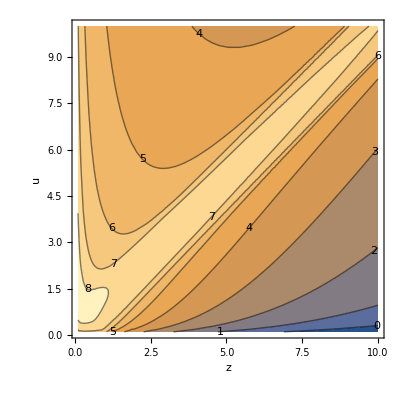

```mathematica
Utilities`ContourTotalParams[FeELOutputDictSIExtrapolatedνn[["fitparams"]]]
```

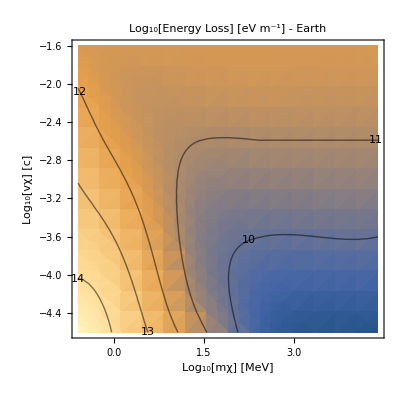

```mathematica
EnergyLoss`PlotEL[FeELOutputDictSIExtrapolatedνn]
```

#### Run SiO2

```mathematica
SiO2OutputDictSI=EnergyLossTableAndInterFITTotalParams[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-2} "c" /.SIConstRepl,<|"mχ"->6,"vχ"->4|>,SiO2Totalparams,True,"SiO2ELOutputDictSI"]
```

1 of 24

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000575531 
Prefactor:	1.33708×10^17
dEdr:	7.69528×10^13

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000219472 
Prefactor:	1.7756×10^17
dEdr:	3.89695×10^13

dEdr total: 1.15922×10^14

2 of 24

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00575483 
Prefactor:	1.33708×10^15
dEdr:	7.69465×10^12

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00219464 
Prefactor:	1.7756×10^15
dEdr:	3.89681×10^12

dEdr total: 1.15915×10^13

3 of 24

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0570879 
Prefactor:	1.33708×10^13
dEdr:	7.63309×10^11

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0218682 
Prefactor:	1.7756×10^13
dEdr:	3.88292×10^11

dEdr total: 1.1516×10^12

4 of 24

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.614583 
Prefactor:	1.33708×10^11
dEdr:	8.21745×10^10

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.208926 
Prefactor:	1.7756×10^11
dEdr:	3.70969×10^10

dEdr total: 1.19271×10^11

5 of 24

For mχ = 4.45×10^-30 , vχ = 7500.
L:	0.0000282836 
Prefactor:	1.33708×10^17
dEdr:	3.78174×10^12

For mχ = 4.45×10^-30 , vχ = 7500.
L:	0.0000120627 
Prefactor:	1.7756×10^17
dEdr:	2.14186×10^12

dEdr total: 5.9236×10^12

6 of 24

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.000286274 
Prefactor:	1.33708×10^15
dEdr:	3.8277×10^11

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.000121194 
Prefactor:	1.7756×10^15
dEdr:	2.15193×10^11

dEdr total: 5.97963×10^11

7 of 24

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.00628915 
Prefactor:	1.33708×10^13
dEdr:	8.40907×10^10

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.00177739 
Prefactor:	1.7756×10^13
dEdr:	3.15593×10^10

dEdr total: 1.1565×10^11

8 of 24

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.781825 
Prefactor:	1.33708×10^11
dEdr:	1.04536×10^11

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.28951 
Prefactor:	1.7756×10^11
dEdr:	5.14054×10^10

dEdr total: 1.55941×10^11

9 of 24

For mχ = 4.45×10^-29 , vχ = 7500.
L:	2.82014×10^-7 
Prefactor:	1.33708×10^17
dEdr:	3.77075×10^10

For mχ = 4.45×10^-29 , vχ = 7500.
L:	1.21145×10^-7 
Prefactor:	1.7756×10^17
dEdr:	2.15105×10^10

dEdr total: 5.9218×10^10

10 of 24

For mχ = 4.45×10^-29 , vχ = 75000.
L:	6.31869×10^-6 
Prefactor:	1.33708×10^15
dEdr:	8.44857×10^9

For mχ = 4.45×10^-29 , vχ = 75000.
L:	1.81103×10^-6 
Prefactor:	1.7756×10^15
dEdr:	3.21567×10^9

dEdr total: 1.16642×10^10

11 of 24

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.0035043 
Prefactor:	1.33708×10^13
dEdr:	4.68552×10^10

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.000611596 
Prefactor:	1.7756×10^13
dEdr:	1.08595×10^10

dEdr total: 5.77147×10^10

12 of 24

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	0.776022 
Prefactor:	1.33708×10^11
dEdr:	1.0376×10^11

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	0.28586 
Prefactor:	1.7756×10^11
dEdr:	5.07573×10^10

dEdr total: 1.54517×10^11

13 of 24

For mχ = 4.45×10^-28 , vχ = 7500.
L:	6.32169×10^-9 
Prefactor:	1.33708×10^17
dEdr:	8.45259×10^8

For mχ = 4.45×10^-28 , vχ = 7500.
L:	1.81186×10^-9 
Prefactor:	1.7756×10^17
dEdr:	3.21714×10^8

dEdr total: 1.16697×10^9

14 of 24

For mχ = 4.45×10^-28 , vχ = 75000.
L:	3.56405×10^-6 
Prefactor:	1.33708×10^15
dEdr:	4.76541×10^9

For mχ = 4.45×10^-28 , vχ = 75000.
L:	6.18331×10^-7 
Prefactor:	1.7756×10^15
dEdr:	1.09791×10^9

dEdr total: 5.86332×10^9

15 of 24

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.00347729 
Prefactor:	1.33708×10^13
dEdr:	4.6494×10^10

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.000600115 
Prefactor:	1.7756×10^13
dEdr:	1.06556×10^10

dEdr total: 5.71496×10^10

16 of 24

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	0.775965 
Prefactor:	1.33708×10^11
dEdr:	1.03752×10^11

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	0.285824 
Prefactor:	1.7756×10^11
dEdr:	5.07509×10^10

dEdr total: 1.54503×10^11

17 of 24

For mχ = 4.45×10^-27 , vχ = 7500.
L:	3.56493×10^-9 
Prefactor:	1.33708×10^17
dEdr:	4.76658×10^8

For mχ = 4.45×10^-27 , vχ = 7500.
L:	6.18408×10^-10 
Prefactor:	1.7756×10^17
dEdr:	1.09805×10^8

dEdr total: 5.86463×10^8

18 of 24

For mχ = 4.45×10^-27 , vχ = 75000.
L:	3.53651×10^-6 
Prefactor:	1.33708×10^15
dEdr:	4.72859×10^9

For mχ = 4.45×10^-27 , vχ = 75000.
L:	6.06403×10^-7 
Prefactor:	1.7756×10^15
dEdr:	1.07673×10^9

dEdr total: 5.80532×10^9

19 of 24

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.00347702 
Prefactor:	1.33708×10^13
dEdr:	4.64904×10^10

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.0006 
Prefactor:	1.7756×10^13
dEdr:	1.06536×10^10

dEdr total: 5.7144×10^10

20 of 24

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	0.775964 
Prefactor:	1.33708×10^11
dEdr:	1.03752×10^11

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	0.285823 
Prefactor:	1.7756×10^11
dEdr:	5.07509×10^10

dEdr total: 1.54503×10^11

21 of 24

For mχ = 4.45×10^-26 , vχ = 7500.
L:	3.53736×10^-9 
Prefactor:	1.33708×10^17
dEdr:	4.72972×10^8

For mχ = 4.45×10^-26 , vχ = 7500.
L:	6.06473×10^-10 
Prefactor:	1.7756×10^17
dEdr:	1.07686×10^8

dEdr total: 5.80658×10^8

22 of 24

For mχ = 4.45×10^-26 , vχ = 75000.
L:	3.53624×10^-6 
Prefactor:	1.33708×10^15
dEdr:	4.72822×10^9

For mχ = 4.45×10^-26 , vχ = 75000.
L:	6.06284×10^-7 
Prefactor:	1.7756×10^15
dEdr:	1.07652×10^9

dEdr total: 5.80474×10^9

23 of 24

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.00347701 
Prefactor:	1.33708×10^13
dEdr:	4.64903×10^10

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.000599999 
Prefactor:	1.7756×10^13
dEdr:	1.06536×10^10

dEdr total: 5.71439×10^10

24 of 24

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	0.775964 
Prefactor:	1.33708×10^11
dEdr:	1.03752×10^11

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	0.285823 
Prefactor:	1.7756×10^11
dEdr:	5.07509×10^10

dEdr total: 1.54503×10^11

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-31,4.45×10^-31,4.45×10^-31,4.45×10^-31},{4.45×10^-30,4.45×10^-30,4.45×10^-30,4.45×10^-30},{4.45×10^-29,4.45×10^-29,4.45×10^-29,4.45×10^-29},{4.45×10^-28,4.45×10^-28,4.45×10^-28,4.45×10^-28},{4.45×10^-27,4.45×10^-27,4.45×10^-27,4.45×10^-27},{4.45×10^-26,4.45×10^-26,4.45×10^-26,4.45×10^-26}},vχMesh→{{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6}},EnergyLossMesh→{{1.15922×10^14,1.15915×10^13,1.1516×10^12,1.19271×10^11},{5.9236×10^12,5.97963×10^11,1.1565×10^11,1.55941×10^11},{5.9218×10^10,1.16642×10^10,5.77147×10^10,1.54517×10^11},{1.16697×10^9,5.86332×10^9,5.71496×10^10,1.54503×10^11},{5.86463×10^8,5.80532×10^9,5.7144×10^10,1.54503×10^11},{5.80658×10^8,5.80474×10^9,5.71439×10^10,1.54503×10^11}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→2.0121×10^30,qF→3.90562×10^10,vF→4.52297×10^6,μ→9.3183×10^-18,ωp→8.0075×10^16,α→1/137,χ→0.392567,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2326.72,nI→2.51512×10^29,Z→8,M→9.27329×10^-26,EF→9.3183×10^-18,ωi→8.0075×10^16,νi→6.06034×10^16,Ai→0.0871584,ωedgei→0}},fname→SiO2ELOutputDictSI,kinlist→<|mχ→{4.45×10^-31,4.45×10^-30,4.45×10^-29,4.45×10^-28,4.45×10^-27,4.45×10^-26},vχ→{7500.,75000.,750000.,7.5×10^6}|>,meshdims→<|mχ→6,vχ→4|>,timesMesh→{{9.73837,8.96029,9.4687,24.6424},{7.28302,7.65099,8.85738,23.7114},{9.53808,9.08678,10.1156,20.6144},{9.03112,9.23114,8.80937,21.2969},{11.4038,10.3027,9.78789,22.466},{9.37322,8.82216,9.6306,21.418}},totalTime→301.24|>

#### Plot SiO2

```mathematica
SiO2OutputDictSI =ReadIt[NotebookDirectory[]<>"SiO2ELOutputDictSI"];
```

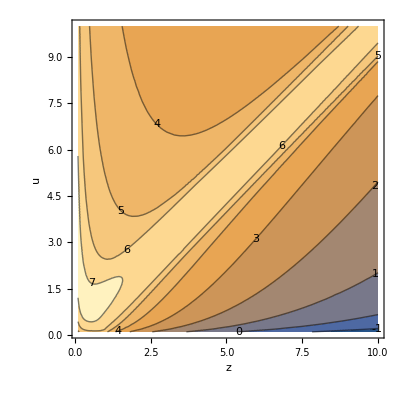

```mathematica
ContourTotalParams[SiO2OutputDictSI[["fitparams"]]]
```

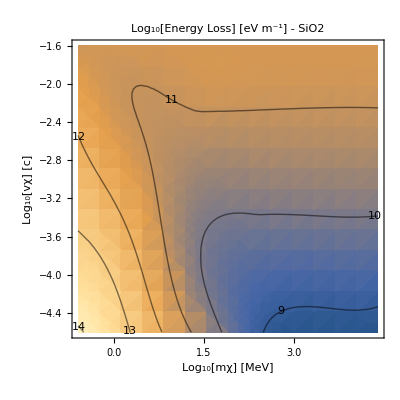

```mathematica
PlotEL[SiO2OutputDictSI,"SiO2"]
```

#### Run MgO

```mathematica
MgOELOutputDictSI=EnergyLossTableAndInterFITTotalParams[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-2} "c" /.SIConstRepl,<|"mχ"->6,"vχ"->4|>,MgOTotalparams,True,"MgOELOutputDictSI"]
```

1 of 24

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.00112953 
Prefactor:	2.55483×10^15
dEdr:	2.88576×10^12

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000687238 
Prefactor:	3.67306×10^16
dEdr:	2.52427×10^13

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000612514 
Prefactor:	2.56623×10^16
dEdr:	1.57185×10^13

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000213441 
Prefactor:	6.41787×10^17
dEdr:	1.36984×10^14

dEdr total: 1.8083×10^14

2 of 24

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.0112938 
Prefactor:	2.55483×10^13
dEdr:	2.88538×10^11

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00687184 
Prefactor:	3.67306×10^14
dEdr:	2.52407×10^12

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00612471 
Prefactor:	2.56623×10^14
dEdr:	1.57174×10^12

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00213433 
Prefactor:	6.41787×10^15
dEdr:	1.36979×10^13

dEdr total: 1.80822×10^13

3 of 24

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.111502 
Prefactor:	2.55483×10^11
dEdr:	2.84868×10^10

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0681819 
Prefactor:	3.67306×10^12
dEdr:	2.50436×10^11

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0608222 
Prefactor:	2.56623×10^12
dEdr:	1.56084×10^11

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0212669 
Prefactor:	6.41787×10^13
dEdr:	1.36488×10^12

dEdr total: 1.79989×10^12

4 of 24

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	1.15755 
Prefactor:	2.55483×10^9
dEdr:	2.95734×10^9

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.738288 
Prefactor:	3.67306×10^10
dEdr:	2.71178×10^10

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.661313 
Prefactor:	2.56623×10^10
dEdr:	1.69708×10^10

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.214381 
Prefactor:	6.41787×10^11
dEdr:	1.37587×10^11

dEdr total: 1.84633×10^11

5 of 24

For mχ = 4.45×10^-30 , vχ = 7500.
L:	0.0000416466 
Prefactor:	2.55483×10^15
dEdr:	1.064×10^11

For mχ = 4.45×10^-30 , vχ = 7500.
L:	0.0000263756 
Prefactor:	3.67306×10^16
dEdr:	9.68792×10^11

For mχ = 4.45×10^-30 , vχ = 7500.
L:	0.0000236944 
Prefactor:	2.56623×10^16
dEdr:	6.08052×10^11

For mχ = 4.45×10^-30 , vχ = 7500.
L:	0.000016343 
Prefactor:	6.41787×10^17
dEdr:	1.04887×10^13

dEdr total: 1.2172×10^13

6 of 24

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.000426044 
Prefactor:	2.55483×10^13
dEdr:	1.08847×10^10

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.000267313 
Prefactor:	3.67306×10^14
dEdr:	9.81857×10^10

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.00023977 
Prefactor:	2.56623×10^14
dEdr:	6.15305×10^10

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.000164302 
Prefactor:	6.41787×10^15
dEdr:	1.05447×10^12

dEdr total: 1.22507×10^12

7 of 24

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.0138112 
Prefactor:	2.55483×10^11
dEdr:	3.52852×10^9

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.0062169 
Prefactor:	3.67306×10^12
dEdr:	2.2835×10^10

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.00521394 
Prefactor:	2.56623×10^12
dEdr:	1.33802×10^10

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.00250297 
Prefactor:	6.41787×10^13
dEdr:	1.60638×10^11

dEdr total: 2.00381×10^11

8 of 24

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	1.39066 
Prefactor:	2.55483×10^9
dEdr:	3.5529×10^9

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.916231 
Prefactor:	3.67306×10^10
dEdr:	3.36537×10^10

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.82923 
Prefactor:	2.56623×10^10
dEdr:	2.12799×10^10

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.282074 
Prefactor:	6.41787×10^11
dEdr:	1.81031×10^11

dEdr total: 2.39518×10^11

9 of 24

For mχ = 4.45×10^-29 , vχ = 7500.
L:	4.03501×10^-7 
Prefactor:	2.55483×10^15
dEdr:	1.03088×10^9

For mχ = 4.45×10^-29 , vχ = 7500.
L:	2.54498×10^-7 
Prefactor:	3.67306×10^16
dEdr:	9.34786×10^9

For mχ = 4.45×10^-29 , vχ = 7500.
L:	2.28513×10^-7 
Prefactor:	2.56623×10^16
dEdr:	5.86416×10^9

For mχ = 4.45×10^-29 , vχ = 7500.
L:	1.67649×10^-7 
Prefactor:	6.41787×10^17
dEdr:	1.07595×10^11

dEdr total: 1.23838×10^11

10 of 24

For mχ = 4.45×10^-29 , vχ = 75000.
L:	0.0000128971 
Prefactor:	2.55483×10^13
dEdr:	3.295×10^8

For mχ = 4.45×10^-29 , vχ = 75000.
L:	5.90339×10^-6 
Prefactor:	3.67306×10^14
dEdr:	2.16835×10^9

For mχ = 4.45×10^-29 , vχ = 75000.
L:	4.96489×10^-6 
Prefactor:	2.56623×10^14
dEdr:	1.2741×10^9

For mχ = 4.45×10^-29 , vχ = 75000.
L:	2.67607×10^-6 
Prefactor:	6.41787×10^15
dEdr:	1.71746×10^10

dEdr total: 2.09466×10^10

11 of 24

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.00907189 
Prefactor:	2.55483×10^11
dEdr:	2.31771×10^9

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.00342466 
Prefactor:	3.67306×10^12
dEdr:	1.2579×10^10

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.00273322 
Prefactor:	2.56623×10^12
dEdr:	7.01407×10^9

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.000999794 
Prefactor:	6.41787×10^13
dEdr:	6.41654×10^10

dEdr total: 8.60762×10^10

12 of 24

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	1.38256 
Prefactor:	2.55483×10^9
dEdr:	3.53222×10^9

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	0.910203 
Prefactor:	3.67306×10^10
dEdr:	3.34323×10^10

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	0.823603 
Prefactor:	2.56623×10^10
dEdr:	2.11355×10^10

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	0.27783 
Prefactor:	6.41787×10^11
dEdr:	1.78308×10^11

dEdr total: 2.36408×10^11

13 of 24

For mχ = 4.45×10^-28 , vχ = 7500.
L:	1.28937×10^-8 
Prefactor:	2.55483×10^15
dEdr:	3.29414×10^7

For mχ = 4.45×10^-28 , vχ = 7500.
L:	5.90278×10^-9 
Prefactor:	3.67306×10^16
dEdr:	2.16813×10^8

For mχ = 4.45×10^-28 , vχ = 7500.
L:	4.96447×10^-9 
Prefactor:	2.56623×10^16
dEdr:	1.274×10^8

For mχ = 4.45×10^-28 , vχ = 7500.
L:	2.67841×10^-9 
Prefactor:	6.41787×10^17
dEdr:	1.71897×10^9

dEdr total: 2.09612×10^9

14 of 24

For mχ = 4.45×10^-28 , vχ = 75000.
L:	8.98801×10^-6 
Prefactor:	2.55483×10^13
dEdr:	2.29628×10^8

For mχ = 4.45×10^-28 , vχ = 75000.
L:	3.41713×10^-6 
Prefactor:	3.67306×10^14
dEdr:	1.25513×10^9

For mχ = 4.45×10^-28 , vχ = 75000.
L:	2.72927×10^-6 
Prefactor:	2.56623×10^14
dEdr:	7.00394×10^8

For mχ = 4.45×10^-28 , vχ = 75000.
L:	1.02799×10^-6 
Prefactor:	6.41787×10^15
dEdr:	6.59749×10^9

dEdr total: 8.78264×10^9

15 of 24

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.00902626 
Prefactor:	2.55483×10^11
dEdr:	2.30606×10^9

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.00339784 
Prefactor:	3.67306×10^12
dEdr:	1.24805×10^10

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.0027094 
Prefactor:	2.56623×10^12
dEdr:	6.95293×10^9

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.000984702 
Prefactor:	6.41787×10^13
dEdr:	6.31968×10^10

dEdr total: 8.49363×10^10

16 of 24

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	1.38249 
Prefactor:	2.55483×10^9
dEdr:	3.53202×10^9

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	0.910135 
Prefactor:	3.67306×10^10
dEdr:	3.34298×10^10

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	0.823548 
Prefactor:	2.56623×10^10
dEdr:	2.11341×10^10

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	0.277789 
Prefactor:	6.41787×10^11
dEdr:	1.78281×10^11

dEdr total: 2.36377×10^11

17 of 24

For mχ = 4.45×10^-27 , vχ = 7500.
L:	8.98917×10^-9 
Prefactor:	2.55483×10^15
dEdr:	2.29658×10^7

For mχ = 4.45×10^-27 , vχ = 7500.
L:	3.41755×10^-9 
Prefactor:	3.67306×10^16
dEdr:	1.25528×10^8

For mχ = 4.45×10^-27 , vχ = 7500.
L:	2.72959×10^-9 
Prefactor:	2.56623×10^16
dEdr:	7.00474×10^7

For mχ = 4.45×10^-27 , vχ = 7500.
L:	1.02829×10^-9 
Prefactor:	6.41787×10^17
dEdr:	6.5994×10^8

dEdr total: 8.78482×10^8

18 of 24

For mχ = 4.45×10^-27 , vχ = 75000.
L:	8.94894×10^-6 
Prefactor:	2.55483×10^13
dEdr:	2.2863×10^8

For mχ = 4.45×10^-27 , vχ = 75000.
L:	3.39228×10^-6 
Prefactor:	3.67306×10^14
dEdr:	1.246×10^9

For mχ = 4.45×10^-27 , vχ = 75000.
L:	2.70693×10^-6 
Prefactor:	2.56623×10^14
dEdr:	6.94659×10^8

For mχ = 4.45×10^-27 , vχ = 75000.
L:	1.0115×10^-6 
Prefactor:	6.41787×10^15
dEdr:	6.49169×10^9

dEdr total: 8.66098×10^9

19 of 24

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.00902581 
Prefactor:	2.55483×10^11
dEdr:	2.30594×10^9

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.00339757 
Prefactor:	3.67306×10^12
dEdr:	1.24795×10^10

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.00270916 
Prefactor:	2.56623×10^12
dEdr:	6.95232×10^9

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.000984551 
Prefactor:	6.41787×10^13
dEdr:	6.31871×10^10

dEdr total: 8.49249×10^10

20 of 24

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	1.38248 
Prefactor:	2.55483×10^9
dEdr:	3.53201×10^9

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	0.910143 
Prefactor:	3.67306×10^10
dEdr:	3.34301×10^10

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	0.823548 
Prefactor:	2.56623×10^10
dEdr:	2.11341×10^10

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	0.277788 
Prefactor:	6.41787×10^11
dEdr:	1.78281×10^11

dEdr total: 2.36377×10^11

21 of 24

For mχ = 4.45×10^-26 , vχ = 7500.
L:	8.95012×10^-9 
Prefactor:	2.55483×10^15
dEdr:	2.2866×10^7

For mχ = 4.45×10^-26 , vχ = 7500.
L:	3.39269×10^-9 
Prefactor:	3.67306×10^16
dEdr:	1.24616×10^8

For mχ = 4.45×10^-26 , vχ = 7500.
L:	2.70724×10^-9 
Prefactor:	2.56623×10^16
dEdr:	6.94739×10^7

For mχ = 4.45×10^-26 , vχ = 7500.
L:	1.01178×10^-9 
Prefactor:	6.41787×10^17
dEdr:	6.4935×10^8

dEdr total: 8.66305×10^8

22 of 24

For mχ = 4.45×10^-26 , vχ = 75000.
L:	8.94855×10^-6 
Prefactor:	2.55483×10^13
dEdr:	2.2862×10^8

For mχ = 4.45×10^-26 , vχ = 75000.
L:	3.39203×10^-6 
Prefactor:	3.67306×10^14
dEdr:	1.24591×10^9

For mχ = 4.45×10^-26 , vχ = 75000.
L:	2.7067×10^-6 
Prefactor:	2.56623×10^14
dEdr:	6.94602×10^8

For mχ = 4.45×10^-26 , vχ = 75000.
L:	1.01134×10^-6 
Prefactor:	6.41787×10^15
dEdr:	6.49063×10^9

dEdr total: 8.65977×10^9

23 of 24

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.0090258 
Prefactor:	2.55483×10^11
dEdr:	2.30594×10^9

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.00339757 
Prefactor:	3.67306×10^12
dEdr:	1.24795×10^10

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.00270916 
Prefactor:	2.56623×10^12
dEdr:	6.95231×10^9

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.000984549 
Prefactor:	6.41787×10^13
dEdr:	6.3187×10^10

dEdr total: 8.49248×10^10

24 of 24

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	1.38248 
Prefactor:	2.55483×10^9
dEdr:	3.53201×10^9

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	0.910143 
Prefactor:	3.67306×10^10
dEdr:	3.34301×10^10

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	0.823548 
Prefactor:	2.56623×10^10
dEdr:	2.11341×10^10

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	0.277788 
Prefactor:	6.41787×10^11
dEdr:	1.78281×10^11

dEdr total: 2.36377×10^11

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-31,4.45×10^-31,4.45×10^-31,4.45×10^-31},{4.45×10^-30,4.45×10^-30,4.45×10^-30,4.45×10^-30},{4.45×10^-29,4.45×10^-29,4.45×10^-29,4.45×10^-29},{4.45×10^-28,4.45×10^-28,4.45×10^-28,4.45×10^-28},{4.45×10^-27,4.45×10^-27,4.45×10^-27,4.45×10^-27},{4.45×10^-26,4.45×10^-26,4.45×10^-26,4.45×10^-26}},vχMesh→{{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6}},EnergyLossMesh→{{1.8083×10^14,1.80822×10^13,1.79989×10^12,1.84633×10^11},{1.2172×10^13,1.22507×10^12,2.00381×10^11,2.39518×10^11},{1.23838×10^11,2.09466×10^10,8.60762×10^10,2.36408×10^11},{2.09612×10^9,8.78264×10^9,8.49363×10^10,2.36377×10^11},{8.78482×10^8,8.66098×10^9,8.49249×10^10,2.36377×10^11},{8.66305×10^8,8.65977×10^9,8.49248×10^10,2.36377×10^11}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.50385×10^29,qF→1.64516×10^10,vF→1.90521×10^6,μ→1.65338×10^-18,ωp→2.18914×10^16,α→1/137,χ→0.604859,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→412.839,nI→1.87981×10^28,Z→8,M→9.27329×10^-26,EF→1.65338×10^-18,ωi→2.18914×10^16,νi→4.25006×10^15,Ai→0.039834,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.58115×10^29,qF→2.19692×10^10,vF→2.54418×10^6,μ→2.94839×10^-18,ωp→3.37819×10^16,α→1/137,χ→0.523421,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→736.197,nI→4.47644×10^28,Z→8,M→9.27329×10^-26,EF→2.94839×10^-18,ωi→3.37819×10^16,νi→5.06751×10^15,Ai→0.180092,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.37351×10^29,qF→2.34828×10^10,vF→2.71947×10^6,μ→3.36866×10^-18,ωp→3.73325×10^16,α→1/137,χ→0.506271,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→841.135,nI→5.46689×10^28,Z→8,M→9.27329×10^-26,EF→3.36866×10^-18,ωi→3.73325×10^16,νi→5.23006×10^15,Ai→0.0963866,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.61838×10^30,qF→3.63218×10^10,vF→4.20631×10^6,μ→8.05919×10^-18,ωp→7.18146×10^16,α→1/137,χ→0.407075,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2012.33,nI→2.02298×10^29,Z→8,M→9.27329×10^-26,EF→8.05919×10^-18,ωi→7.18146×10^16,νi→1.12397×10^17,Ai→0.421157,ωedgei→0}},fname→MgOELOutputDictSI,kinlist→<|mχ→{4.45×10^-31,4.45×10^-30,4.45×10^-29,4.45×10^-28,4.45×10^-27,4.45×10^-26},vχ→{7500.,75000.,750000.,7.5×10^6}|>,meshdims→<|mχ→6,vχ→4|>,timesMesh→{{17.4923,17.3714,19.7093,86.6003},{18.2579,17.911,21.5942,85.1463},{20.0719,20.4824,25.7837,83.331},{22.6371,22.4279,26.4989,75.8962},{22.6305,21.8721,26.8029,82.1525},{20.4463,19.4634,26.8931,83.8745}},totalTime→885.347|>

#### Plot MgO

```mathematica
MgOOutputDictSI =ReadIt[NotebookDirectory[]<>"MgOELOutputDictSI"];
```

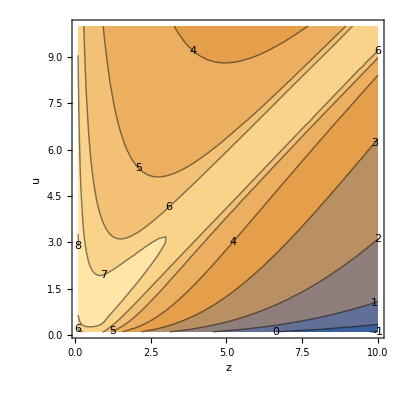

```mathematica
ContourTotalParams[MgOOutputDictSI[["fitparams"]]]
```

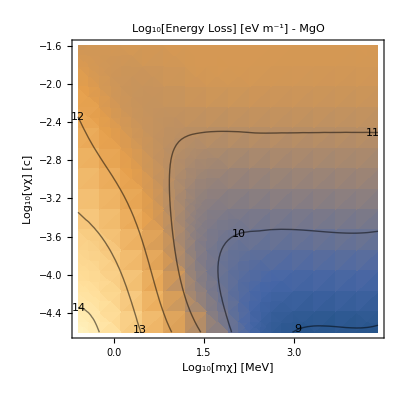

```mathematica
PlotEL[MgOOutputDictSI,"MgO"]
```

#### Run Iron with the temperature enhancement.

```mathematica
FeELOutputDictSIEnhanced = EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-2} "c" /.SIConstRepl,<|"mχ"->6,"vχ"->4|>,FeTotalparams,True,"FeELOutputDictSIEnhanced"]
```

1 of 24

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.00116074 
Prefactor:	8.19529×10^15
dEdr:	9.5126×10^12

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000940039 
Prefactor:	6.19052×10^15
dEdr:	5.81933×10^12

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000559998 
Prefactor:	1.01998×10^17
dEdr:	5.71185×10^13

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000162759 
Prefactor:	8.78553×10^17
dEdr:	1.42992×10^14

For mχ = 4.45×10^-31 , vχ = 7500.
L:	9.33024×10^-6 
Prefactor:	4.79324×10^18
dEdr:	4.47221×10^13

For mχ = 4.45×10^-31 , vχ = 7500.
L:	5.34975×10^-7 
Prefactor:	3.10619×10^18
dEdr:	1.66173×10^12

dEdr total: 2.61827×10^14

2 of 24

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.0116058 
Prefactor:	8.19529×10^13
dEdr:	9.51128×10^11

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00939926 
Prefactor:	6.19052×10^13
dEdr:	5.81863×10^11

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00559954 
Prefactor:	1.01998×10^15
dEdr:	5.7114×10^12

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00162754 
Prefactor:	8.78553×10^15
dEdr:	1.42988×10^13

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.0000933023 
Prefactor:	4.79324×10^16
dEdr:	4.47221×10^12

For mχ = 4.45×10^-31 , vχ = 75000.
L:	5.34975×10^-6 
Prefactor:	3.10619×10^16
dEdr:	1.66173×10^11

dEdr total: 2.61816×10^13

3 of 24

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.114579 
Prefactor:	8.19529×10^11
dEdr:	9.39006×10^10

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0929053 
Prefactor:	6.19052×10^11
dEdr:	5.75132×10^10

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0555615 
Prefactor:	1.01998×10^13
dEdr:	5.66714×10^11

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0162292 
Prefactor:	8.78553×10^13
dEdr:	1.42582×10^12

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.000932943 
Prefactor:	4.79324×10^14
dEdr:	4.47182×10^11

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0000534978 
Prefactor:	3.10619×10^14
dEdr:	1.66174×10^10

dEdr total: 2.60775×10^12

4 of 24

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	1.20534 
Prefactor:	8.19529×10^9
dEdr:	9.87812×10^9

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.982206 
Prefactor:	6.19052×10^9
dEdr:	6.08037×10^9

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.597842 
Prefactor:	1.01998×10^11
dEdr:	6.09785×10^10

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.151339 
Prefactor:	8.78553×10^11
dEdr:	1.32959×10^11

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.00924909 
Prefactor:	4.79324×10^12
dEdr:	4.43331×10^10

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.000535251 
Prefactor:	3.10619×10^12
dEdr:	1.66259×10^9

dEdr total: 2.55892×10^11

5 of 24

For mχ = 4.45×10^-30 , vχ = 7500.
L:	0.0000662786 
Prefactor:	8.19529×10^15
dEdr:	5.43172×10^11

For mχ = 4.45×10^-30 , vχ = 7500.
L:	0.0000392174 
Prefactor:	6.19052×10^15
dEdr:	2.42776×10^11

For mχ = 4.45×10^-30 , vχ = 7500.
L:	0.0000269417 
Prefactor:	1.01998×10^17
dEdr:	2.74799×10^12

For mχ = 4.45×10^-30 , vχ = 7500.
L:	9.58557×10^-6 
Prefactor:	8.78553×10^17
dEdr:	8.42144×10^12

For mχ = 4.45×10^-30 , vχ = 7500.
L:	4.51478×10^-7 
Prefactor:	4.79324×10^18
dEdr:	2.16404×10^12

For mχ = 4.45×10^-30 , vχ = 7500.
L:	2.2785×10^-8 
Prefactor:	3.10619×10^18
dEdr:	7.07744×10^10

dEdr total: 1.41902×10^13

6 of 24

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.000680666 
Prefactor:	8.19529×10^13
dEdr:	5.57825×10^10

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.000399797 
Prefactor:	6.19052×10^13
dEdr:	2.47495×10^10

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.000272572 
Prefactor:	1.01998×10^15
dEdr:	2.78017×10^11

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.0000962013 
Prefactor:	8.78553×10^15
dEdr:	8.45179×10^11

For mχ = 4.45×10^-30 , vχ = 75000.
L:	4.51571×10^-6 
Prefactor:	4.79324×10^16
dEdr:	2.16449×10^11

For mχ = 4.45×10^-30 , vχ = 75000.
L:	2.27853×10^-7 
Prefactor:	3.10619×10^16
dEdr:	7.07753×10^9

dEdr total: 1.42725×10^12

7 of 24

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.0242272 
Prefactor:	8.19529×10^11
dEdr:	1.98549×10^10

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.0116092 
Prefactor:	6.19052×10^11
dEdr:	7.18668×10^9

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.00587189 
Prefactor:	1.01998×10^13
dEdr:	5.98919×10^10

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.00130646 
Prefactor:	8.78553×10^13
dEdr:	1.14779×10^11

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.0000460829 
Prefactor:	4.79324×10^14
dEdr:	2.20887×10^10

For mχ = 4.45×10^-30 , vχ = 750000.
L:	2.28155×10^-6 
Prefactor:	3.10619×10^14
dEdr:	7.08693×10^8

dEdr total: 2.2451×10^11

8 of 24

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	1.46572 
Prefactor:	8.19529×10^9
dEdr:	1.2012×10^10

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	1.19748 
Prefactor:	6.19052×10^9
dEdr:	7.413×10^9

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.762186 
Prefactor:	1.01998×10^11
dEdr:	7.77412×10^10

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.198633 
Prefactor:	8.78553×10^11
dEdr:	1.74509×10^11

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.00137738 
Prefactor:	4.79324×10^12
dEdr:	6.6021×10^9

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.0000258405 
Prefactor:	3.10619×10^12
dEdr:	8.02654×10^7

dEdr total: 2.78358×10^11

9 of 24

For mχ = 4.45×10^-29 , vχ = 7500.
L:	6.74067×10^-7 
Prefactor:	8.19529×10^15
dEdr:	5.52417×10^9

For mχ = 4.45×10^-29 , vχ = 7500.
L:	3.86345×10^-7 
Prefactor:	6.19052×10^15
dEdr:	2.39168×10^9

For mχ = 4.45×10^-29 , vχ = 7500.
L:	2.68082×10^-7 
Prefactor:	1.01998×10^17
dEdr:	2.73438×10^10

For mχ = 4.45×10^-29 , vχ = 7500.
L:	9.67645×10^-8 
Prefactor:	8.78553×10^17
dEdr:	8.50128×10^10

For mχ = 4.45×10^-29 , vχ = 7500.
L:	4.51879×10^-9 
Prefactor:	4.79324×10^18
dEdr:	2.16596×10^10

For mχ = 4.45×10^-29 , vχ = 7500.
L:	2.26213×10^-10 
Prefactor:	3.10619×10^18
dEdr:	7.02661×10^8

dEdr total: 1.42635×10^11

10 of 24

For mχ = 4.45×10^-29 , vχ = 75000.
L:	0.0000253134 
Prefactor:	8.19529×10^13
dEdr:	2.07451×10^9

For mχ = 4.45×10^-29 , vχ = 75000.
L:	0.0000112281 
Prefactor:	6.19052×10^13
dEdr:	6.9508×10^8

For mχ = 4.45×10^-29 , vχ = 75000.
L:	5.87609×10^-6 
Prefactor:	1.01998×10^15
dEdr:	5.99348×10^9

For mχ = 4.45×10^-29 , vχ = 75000.
L:	1.33953×10^-6 
Prefactor:	8.78553×10^15
dEdr:	1.17685×10^10

For mχ = 4.45×10^-29 , vχ = 75000.
L:	4.61524×10^-8 
Prefactor:	4.79324×10^16
dEdr:	2.21219×10^9

For mχ = 4.45×10^-29 , vχ = 75000.
L:	2.26523×10^-9 
Prefactor:	3.10619×10^16
dEdr:	7.03623×10^7

dEdr total: 2.28141×10^10

11 of 24

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.0179296 
Prefactor:	8.19529×10^11
dEdr:	1.46938×10^10

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.00742999 
Prefactor:	6.19052×10^11
dEdr:	4.59955×10^9

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.00320711 
Prefactor:	1.01998×10^13
dEdr:	3.27118×10^10

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.000381819 
Prefactor:	8.78553×10^13
dEdr:	3.35448×10^10

For mχ = 4.45×10^-29 , vχ = 750000.
L:	1.42583×10^-6 
Prefactor:	4.79324×10^14
dEdr:	6.83434×10^8

For mχ = 4.45×10^-29 , vχ = 750000.
L:	2.57489×10^-8 
Prefactor:	3.10619×10^14
dEdr:	7.9981×10^6

dEdr total: 8.62414×10^10

12 of 24

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	1.45653 
Prefactor:	8.19529×10^9
dEdr:	1.19367×10^10

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	1.19001 
Prefactor:	6.19052×10^9
dEdr:	7.36678×10^9

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	0.756514 
Prefactor:	1.01998×10^11
dEdr:	7.71627×10^10

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	0.195231 
Prefactor:	8.78553×10^11
dEdr:	1.71521×10^11

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	0.000962787 
Prefactor:	4.79324×10^12
dEdr:	4.61487×10^9

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	3.35284×10^-6 
Prefactor:	3.10619×10^12
dEdr:	1.04145×10^7

dEdr total: 2.72612×10^11

13 of 24

For mχ = 4.45×10^-28 , vχ = 7500.
L:	2.53368×10^-8 
Prefactor:	8.19529×10^15
dEdr:	2.07642×10^8

For mχ = 4.45×10^-28 , vχ = 7500.
L:	1.12304×10^-8 
Prefactor:	6.19052×10^15
dEdr:	6.95219×10^7

For mχ = 4.45×10^-28 , vχ = 7500.
L:	5.8787×10^-9 
Prefactor:	1.01998×10^17
dEdr:	5.99614×10^8

For mχ = 4.45×10^-28 , vχ = 7500.
L:	1.34016×10^-9 
Prefactor:	8.78553×10^17
dEdr:	1.1774×10^9

For mχ = 4.45×10^-28 , vχ = 7500.
L:	4.61638×10^-11 
Prefactor:	4.79324×10^18
dEdr:	2.21274×10^8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00006}. NIntegrate obtained 2.26569×10^-12 and 3.86375×10^-18 for the integral and error estimates.

For mχ = 4.45×10^-28 , vχ = 7500.
L:	2.26569×10^-12 
Prefactor:	3.10619×10^18
dEdr:	7.03767×10^6

dEdr total: 2.28249×10^9

14 of 24

For mχ = 4.45×10^-28 , vχ = 75000.
L:	0.0000188376 
Prefactor:	8.19529×10^13
dEdr:	1.5438×10^9

For mχ = 4.45×10^-28 , vχ = 75000.
L:	7.47826×10^-6 
Prefactor:	6.19052×10^13
dEdr:	4.62943×10^8

For mχ = 4.45×10^-28 , vχ = 75000.
L:	3.25609×10^-6 
Prefactor:	1.01998×10^15
dEdr:	3.32114×10^9

For mχ = 4.45×10^-28 , vχ = 75000.
L:	3.85727×10^-7 
Prefactor:	8.78553×10^15
dEdr:	3.38882×10^9

For mχ = 4.45×10^-28 , vχ = 75000.
L:	1.42703×10^-9 
Prefactor:	4.79324×10^16
dEdr:	6.84011×10^7

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00006}. NIntegrate obtained 2.57553×10^-11 and 2.73265×10^-17 for the integral and error estimates.

For mχ = 4.45×10^-28 , vχ = 75000.
L:	2.57553×10^-11 
Prefactor:	3.10619×10^16
dEdr:	800009.

dEdr total: 8.7859×10^9

15 of 24

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.0178683 
Prefactor:	8.19529×10^11
dEdr:	1.46436×10^10

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.00738969 
Prefactor:	6.19052×10^11
dEdr:	4.5746×10^9

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.00318128 
Prefactor:	1.01998×10^13
dEdr:	3.24483×10^10

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.000372636 
Prefactor:	8.78553×10^13
dEdr:	3.27381×10^10

For mχ = 4.45×10^-28 , vχ = 750000.
L:	9.79427×10^-7 
Prefactor:	4.79324×10^14
dEdr:	4.69463×10^8

For mχ = 4.45×10^-28 , vχ = 750000.
L:	3.35591×10^-9 
Prefactor:	3.10619×10^14
dEdr:	1.04241×10^6

dEdr total: 8.4875×10^10

16 of 24

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	1.45644 
Prefactor:	8.19529×10^9
dEdr:	1.19359×10^10

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	1.18994 
Prefactor:	6.19052×10^9
dEdr:	7.36633×10^9

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	0.756458 
Prefactor:	1.01998×10^11
dEdr:	7.7157×10^10

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	0.195198 
Prefactor:	8.78553×10^11
dEdr:	1.71492×10^11

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	0.000958704 
Prefactor:	4.79324×10^12
dEdr:	4.5953×10^9

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	3.13014×10^-6 
Prefactor:	3.10619×10^12
dEdr:	9.72281×10^6

dEdr total: 2.72556×10^11

17 of 24

For mχ = 4.45×10^-27 , vχ = 7500.
L:	1.885×10^-8 
Prefactor:	8.19529×10^15
dEdr:	1.54481×10^8

For mχ = 4.45×10^-27 , vχ = 7500.
L:	7.48007×10^-9 
Prefactor:	6.19052×10^15
dEdr:	4.63055×10^7

For mχ = 4.45×10^-27 , vχ = 7500.
L:	3.25683×10^-9 
Prefactor:	1.01998×10^17
dEdr:	3.3219×10^8

For mχ = 4.45×10^-27 , vχ = 7500.
L:	3.8577×10^-10 
Prefactor:	8.78553×10^17
dEdr:	3.38919×10^8

For mχ = 4.45×10^-27 , vχ = 7500.
L:	1.42705×10^-12 
Prefactor:	4.79324×10^18
dEdr:	6.84018×10^6

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00006}. NIntegrate obtained 2.57554×10^-14 and 2.76681×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-27 , vχ = 7500.
L:	2.57554×10^-14 
Prefactor:	3.10619×10^18
dEdr:	80001.1

dEdr total: 8.78815×10^8

18 of 24

For mχ = 4.45×10^-27 , vχ = 75000.
L:	0.0000187729 
Prefactor:	8.19529×10^13
dEdr:	1.53849×10^9

For mχ = 4.45×10^-27 , vχ = 75000.
L:	7.44077×10^-6 
Prefactor:	6.19052×10^13
dEdr:	4.60622×10^8

For mχ = 4.45×10^-27 , vχ = 75000.
L:	3.22989×10^-6 
Prefactor:	1.01998×10^15
dEdr:	3.29442×10^9

For mχ = 4.45×10^-27 , vχ = 75000.
L:	3.76188×10^-7 
Prefactor:	8.78553×10^15
dEdr:	3.30501×10^9

For mχ = 4.45×10^-27 , vχ = 75000.
L:	9.79675×10^-10 
Prefactor:	4.79324×10^16
dEdr:	4.69582×10^7

For mχ = 4.45×10^-27 , vχ = 75000.
L:	3.35596×10^-12 
Prefactor:	3.10619×10^16
dEdr:	104242.

dEdr total: 8.6456×10^9

19 of 24

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.0178676 
Prefactor:	8.19529×10^11
dEdr:	1.4643×10^10

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.00738929 
Prefactor:	6.19052×10^11
dEdr:	4.57435×10^9

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.00318102 
Prefactor:	1.01998×10^13
dEdr:	3.24457×10^10

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.000372544 
Prefactor:	8.78553×10^13
dEdr:	3.273×10^10

For mχ = 4.45×10^-27 , vχ = 750000.
L:	9.74962×10^-7 
Prefactor:	4.79324×10^14
dEdr:	4.67323×10^8

For mχ = 4.45×10^-27 , vχ = 750000.
L:	3.13194×10^-9 
Prefactor:	3.10619×10^14
dEdr:	972839.

dEdr total: 8.48614×10^10

20 of 24

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	1.45644 
Prefactor:	8.19529×10^9
dEdr:	1.19359×10^10

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	1.18994 
Prefactor:	6.19052×10^9
dEdr:	7.36633×10^9

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	0.756458 
Prefactor:	1.01998×10^11
dEdr:	7.71569×10^10

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	0.195197 
Prefactor:	8.78553×10^11
dEdr:	1.71491×10^11

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	0.000958663 
Prefactor:	4.79324×10^12
dEdr:	4.59511×10^9

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	3.12791×10^-6 
Prefactor:	3.10619×10^12
dEdr:	9.71589×10^6

dEdr total: 2.72555×10^11

21 of 24

For mχ = 4.45×10^-26 , vχ = 7500.
L:	1.87851×10^-8 
Prefactor:	8.19529×10^15
dEdr:	1.53949×10^8

For mχ = 4.45×10^-26 , vχ = 7500.
L:	7.44257×10^-9 
Prefactor:	6.19052×10^15
dEdr:	4.60733×10^7

For mχ = 4.45×10^-26 , vχ = 7500.
L:	3.23061×10^-9 
Prefactor:	1.01998×10^17
dEdr:	3.29515×10^8

For mχ = 4.45×10^-26 , vχ = 7500.
L:	3.76226×10^-10 
Prefactor:	8.78553×10^17
dEdr:	3.30534×10^8

For mχ = 4.45×10^-26 , vχ = 7500.
L:	9.79677×10^-13 
Prefactor:	4.79324×10^18
dEdr:	4.69583×10^6

For mχ = 4.45×10^-26 , vχ = 7500.
L:	3.35596×10^-15 
Prefactor:	3.10619×10^18
dEdr:	10424.2

dEdr total: 8.64778×10^8

22 of 24

For mχ = 4.45×10^-26 , vχ = 75000.
L:	0.0000187722 
Prefactor:	8.19529×10^13
dEdr:	1.53844×10^9

For mχ = 4.45×10^-26 , vχ = 75000.
L:	7.4404×10^-6 
Prefactor:	6.19052×10^13
dEdr:	4.60599×10^8

For mχ = 4.45×10^-26 , vχ = 75000.
L:	3.22963×10^-6 
Prefactor:	1.01998×10^15
dEdr:	3.29415×10^9

For mχ = 4.45×10^-26 , vχ = 75000.
L:	3.76092×10^-7 
Prefactor:	8.78553×10^15
dEdr:	3.30417×10^9

For mχ = 4.45×10^-26 , vχ = 75000.
L:	9.75201×10^-10 
Prefactor:	4.79324×10^16
dEdr:	4.67438×10^7

For mχ = 4.45×10^-26 , vχ = 75000.
L:	3.13196×10^-12 
Prefactor:	3.10619×10^16
dEdr:	97284.7

dEdr total: 8.6442×10^9

23 of 24

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.0178676 
Prefactor:	8.19529×10^11
dEdr:	1.4643×10^10

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.00738928 
Prefactor:	6.19052×10^11
dEdr:	4.57435×10^9

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.00318102 
Prefactor:	1.01998×10^13
dEdr:	3.24457×10^10

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.000372543 
Prefactor:	8.78553×10^13
dEdr:	3.27299×10^10

For mχ = 4.45×10^-26 , vχ = 750000.
L:	9.74918×10^-7 
Prefactor:	4.79324×10^14
dEdr:	4.67302×10^8

For mχ = 4.45×10^-26 , vχ = 750000.
L:	3.1297×10^-9 
Prefactor:	3.10619×10^14
dEdr:	972144.

dEdr total: 8.48612×10^10

24 of 24

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	1.45644 
Prefactor:	8.19529×10^9
dEdr:	1.19359×10^10

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	1.18994 
Prefactor:	6.19052×10^9
dEdr:	7.36633×10^9

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	0.756458 
Prefactor:	1.01998×10^11
dEdr:	7.71569×10^10

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	0.195197 
Prefactor:	8.78553×10^11
dEdr:	1.71491×10^11

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	0.000958663 
Prefactor:	4.79324×10^12
dEdr:	4.5951×10^9

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	3.12789×10^-6 
Prefactor:	3.10619×10^12
dEdr:	9.71582×10^6

dEdr total: 2.72555×10^11

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-31,4.45×10^-31,4.45×10^-31,4.45×10^-31},{4.45×10^-30,4.45×10^-30,4.45×10^-30,4.45×10^-30},{4.45×10^-29,4.45×10^-29,4.45×10^-29,4.45×10^-29},{4.45×10^-28,4.45×10^-28,4.45×10^-28,4.45×10^-28},{4.45×10^-27,4.45×10^-27,4.45×10^-27,4.45×10^-27},{4.45×10^-26,4.45×10^-26,4.45×10^-26,4.45×10^-26}},vχMesh→{{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6}},EnergyLossMesh→{{2.61827×10^14,2.61816×10^13,2.60775×10^12,2.55892×10^11},{1.41902×10^13,1.42725×10^12,2.2451×10^11,2.78358×10^11},{1.42635×10^11,2.28141×10^10,8.62414×10^10,2.72612×10^11},{2.28249×10^9,8.7859×10^9,8.4875×10^10,2.72556×10^11},{8.78815×10^8,8.6456×10^9,8.48614×10^10,2.72555×10^11},{8.64778×10^8,8.6442×10^9,8.48612×10^10,2.72555×10^11}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00193079,ωedgei→1.09042×10^18},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→2.83087×10^-6,ωedgei→1.09893×10^19}},fname→FeELOutputDictSIEnhanced,kinlist→<|mχ→{4.45×10^-31,4.45×10^-30,4.45×10^-29,4.45×10^-28,4.45×10^-27,4.45×10^-26},vχ→{7500.,75000.,750000.,7.5×10^6}|>,meshdims→<|mχ→6,vχ→4|>,timesMesh→{{70.9727,78.4801,77.7882,195.877},{75.8056,73.5256,40.2285,95.9432},{39.5085,35.9847,39.1477,86.6143},{47.1814,40.8565,42.8881,84.2601},{46.5792,38.2247,77.5395,174.264},{92.1197,92.6672,97.0576,99.9517}},totalTime→1843.47|>

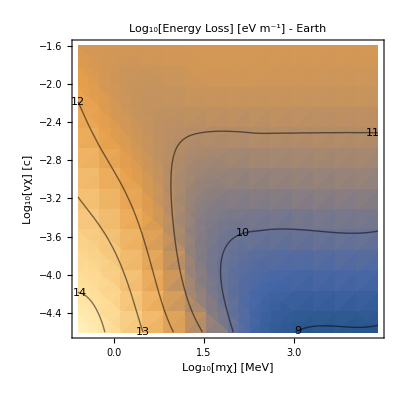

```mathematica
EnergyLoss`PlotEL[FeELOutputDictSIEnhanced]
```

### with wider mass range and temperature enhancement

Also changed velocity bounds so they are above escape velocity while we compute κ_min

```mathematica
vescape
{2 10^-4,2 10^-1} "c" /.SIConstRepl
```

11200

{60000,60000000}

#### Run Iron

```mathematica
FeTotalparamscoreT={{},{},{},{},{},{}};
Do[FeTotalparamscoreT[[i]]=Utilities`ReplaceParams[FeTotalparams[[i]],βcore,"β"],{i,Length[FeTotalparams]}];
```

```mathematica
FeELOutputDictSIEnhanced = EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,FeTotalparamscoreT,True,"FeELOutputDictSIEnhanced"]
```

1 of 32

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1987.19}. NIntegrate obtained 0.000726932 and 6.96831×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000726932 
Prefactor:	1.28051×10^14
dEdr:	9.30847×10^10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.000572148 and 0.0000306585 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000572148 
Prefactor:	9.67268×10^13
dEdr:	5.53421×10^10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {7257.97}. NIntegrate obtained 0.000367893 and 0.00002451 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000367893 
Prefactor:	1.59371×10^15
dEdr:	5.86316×10^11

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.0000994691 
Prefactor:	1.37274×10^16
dEdr:	1.36545×10^12

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 4.45×10^-33 , vχ = 60000
L:	6.05146×10^-6 
Prefactor:	7.48944×10^16
dEdr:	4.53221×10^11

For mχ = 4.45×10^-33 , vχ = 60000
L:	4.44407×10^-7 
Prefactor:	4.85342×10^16
dEdr:	2.15689×10^10

dEdr total: 2.57498×10^12

2 of 32

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00665304 
Prefactor:	1.28051×10^12
dEdr:	8.51931×10^9

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00584032 
Prefactor:	9.67268×10^11
dEdr:	5.64916×10^9

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00311384 
Prefactor:	1.59371×10^13
dEdr:	4.96257×10^10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.000994579 
Prefactor:	1.37274×10^14
dEdr:	1.3653×10^11

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.0000605877 
Prefactor:	7.48944×10^14
dEdr:	4.53768×10^10

For mχ = 4.45×10^-33 , vχ = 600000
L:	4.44412×10^-6 
Prefactor:	4.85342×10^14
dEdr:	2.15692×10^9

dEdr total: 2.47858×10^11

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.072139 
Prefactor:	1.28051×10^10
dEdr:	9.23749×10^8

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0557751 
Prefactor:	9.67268×10^9
dEdr:	5.39495×10^8

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0327272 
Prefactor:	1.59371×10^11
dEdr:	5.21577×10^9

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.00996425 
Prefactor:	1.37274×10^12
dEdr:	1.36783×10^10

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.000608537 
Prefactor:	7.48944×10^12
dEdr:	4.5576×10^9

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0000444473 
Prefactor:	4.85342×10^12
dEdr:	2.15721×10^8

dEdr total: 2.51307×10^10

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.968238 
Prefactor:	1.28051×10^8
dEdr:	1.23984×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.794273 
Prefactor:	9.67268×10^7
dEdr:	7.68275×10^7

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.455748 
Prefactor:	1.59371×10^9
dEdr:	7.26332×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.0994695 
Prefactor:	1.37274×10^10
dEdr:	1.36546×10^9

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.0060994 
Prefactor:	7.48944×10^10
dEdr:	4.56811×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.000444251 
Prefactor:	4.85342×10^10
dEdr:	2.15614×10^7

dEdr total: 2.77097×10^9

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.0032805 
Prefactor:	1.28051×10^14
dEdr:	4.20072×10^11

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.00259534 
Prefactor:	9.67268×10^13
dEdr:	2.51039×10^11

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.00155333 
Prefactor:	1.59371×10^15
dEdr:	2.47557×10^12

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000455359 
Prefactor:	1.37274×10^16
dEdr:	6.25089×10^12

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.0000291223 
Prefactor:	7.48944×10^16
dEdr:	2.1811×10^12

For mχ = 8.5916×10^-32 , vχ = 60000
L:	2.18057×10^-6 
Prefactor:	4.85342×10^16
dEdr:	1.05832×10^11

dEdr total: 1.16845×10^13

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0327605 
Prefactor:	1.28051×10^12
dEdr:	4.19502×10^10

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0259266 
Prefactor:	9.67268×10^11
dEdr:	2.5078×10^10

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0155226 
Prefactor:	1.59371×10^13
dEdr:	2.47386×10^11

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00455241 
Prefactor:	1.37274×10^14
dEdr:	6.24927×10^11

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.000291215 
Prefactor:	7.48944×10^14
dEdr:	2.18104×10^11

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0000218056 
Prefactor:	4.85342×10^14
dEdr:	1.05832×10^10

dEdr total: 1.16803×10^12

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.324957 
Prefactor:	1.28051×10^10
dEdr:	4.16112×10^9

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.242762 
Prefactor:	9.67268×10^9
dEdr:	2.34816×10^9

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.147563 
Prefactor:	1.59371×10^11
dEdr:	2.35172×10^10

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0445003 
Prefactor:	1.37274×10^12
dEdr:	6.10874×10^10

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.00290454 
Prefactor:	7.48944×10^12
dEdr:	2.17534×10^10

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.000217998 
Prefactor:	4.85342×10^12
dEdr:	1.05804×10^9

dEdr total: 1.13925×10^11

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	2.25119 
Prefactor:	1.28051×10^8
dEdr:	2.88268×10^8

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.84363 
Prefactor:	9.67268×10^7
dEdr:	1.78328×10^8

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.26383 
Prefactor:	1.59371×10^9
dEdr:	2.01419×10^9

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.484458 
Prefactor:	1.37274×10^10
dEdr:	6.65035×10^9

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.0296763 
Prefactor:	7.48944×10^10
dEdr:	2.22259×10^9

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.00212576 
Prefactor:	4.85342×10^10
dEdr:	1.03172×10^8

dEdr total: 1.14569×10^10

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00451342 
Prefactor:	1.28051×10^14
dEdr:	5.7795×10^11

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00298544 
Prefactor:	9.67268×10^13
dEdr:	2.88772×10^11

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00190694 
Prefactor:	1.59371×10^15
dEdr:	3.03911×10^12

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000608308 
Prefactor:	1.37274×10^16
dEdr:	8.35048×10^12

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.0000285286 
Prefactor:	7.48944×10^16
dEdr:	2.13663×10^12

For mχ = 1.65878×10^-30 , vχ = 60000
L:	1.44555×10^-6 
Prefactor:	4.85342×10^16
dEdr:	7.01586×10^10

dEdr total: 1.44631×10^13

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0536122 
Prefactor:	1.28051×10^12
dEdr:	6.86511×10^10

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0341173 
Prefactor:	9.67268×10^11
dEdr:	3.30006×10^10

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0206437 
Prefactor:	1.59371×10^13
dEdr:	3.29002×10^11

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.00622205 
Prefactor:	1.37274×10^14
dEdr:	8.54125×10^11

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.000285674 
Prefactor:	7.48944×10^14
dEdr:	2.13954×10^11

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0000144568 
Prefactor:	4.85342×10^14
dEdr:	7.01651×10^9

dEdr total: 1.50575×10^12

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	1.33303 
Prefactor:	1.28051×10^10
dEdr:	1.70696×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	1.08488 
Prefactor:	9.67268×10^9
dEdr:	1.04937×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.670243 
Prefactor:	1.59371×10^11
dEdr:	1.06818×10^11

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.157968 
Prefactor:	1.37274×10^12
dEdr:	2.16849×10^11

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.00324225 
Prefactor:	7.48944×10^12
dEdr:	2.42827×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.000145913 
Prefactor:	4.85342×10^12
dEdr:	7.08177×10^8

dEdr total: 3.76221×10^11

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	3.35067 
Prefactor:	1.28051×10^8
dEdr:	4.29058×10^8

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	2.74005 
Prefactor:	9.67268×10^7
dEdr:	2.65037×10^8

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.94615 
Prefactor:	1.59371×10^9
dEdr:	3.10161×10^9

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.835874 
Prefactor:	1.37274×10^10
dEdr:	1.14744×10^10

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.0987937 
Prefactor:	7.48944×10^10
dEdr:	7.3991×10^9

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.00277327 
Prefactor:	4.85342×10^10
dEdr:	1.34598×10^8

dEdr total: 2.28038×10^10

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	0.0000197241 
Prefactor:	1.28051×10^14
dEdr:	2.5257×10^9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	9.6622×10^-6 
Prefactor:	9.67268×10^13
dEdr:	9.34594×10^8

For mχ = 3.2026×10^-29 , vχ = 60000
L:	5.74276×10^-6 
Prefactor:	1.59371×10^15
dEdr:	9.15231×10^9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	1.6807×10^-6 
Prefactor:	1.37274×10^16
dEdr:	2.30716×10^10

For mχ = 3.2026×10^-29 , vχ = 60000
L:	7.02645×10^-8 
Prefactor:	7.48944×10^16
dEdr:	5.26242×10^9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	3.4951×10^-9 
Prefactor:	4.85342×10^16
dEdr:	1.69632×10^8

dEdr total: 4.11163×10^10

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00938763 
Prefactor:	1.28051×10^12
dEdr:	1.2021×10^10

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00384783 
Prefactor:	9.67268×10^11
dEdr:	3.72188×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.0016762 
Prefactor:	1.59371×10^13
dEdr:	2.67138×10^10

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000205881 
Prefactor:	1.37274×10^14
dEdr:	2.82621×10^10

For mχ = 3.2026×10^-29 , vχ = 600000
L:	1.19602×10^-6 
Prefactor:	7.48944×10^14
dEdr:	8.95752×10^8

For mχ = 3.2026×10^-29 , vχ = 600000
L:	3.65358×10^-8 
Prefactor:	4.85342×10^14
dEdr:	1.77323×10^7

dEdr total: 7.16323×10^10

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	1.25526 
Prefactor:	1.28051×10^10
dEdr:	1.60738×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	1.02208 
Prefactor:	9.67268×10^9
dEdr:	9.88622×10^9

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.622429 
Prefactor:	1.59371×10^11
dEdr:	9.91975×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.127701 
Prefactor:	1.37274×10^12
dEdr:	1.753×10^11

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.000500096 
Prefactor:	7.48944×10^12
dEdr:	3.74544×10^9

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	1.94984×10^-6 
Prefactor:	4.85342×10^12
dEdr:	9.46339×10^6

dEdr total: 3.04212×10^11

16 of 32

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	3.27304 
Prefactor:	1.28051×10^8
dEdr:	4.19117×10^8

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	2.67676 
Prefactor:	9.67268×10^7
dEdr:	2.58915×10^8

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.89797 
Prefactor:	1.59371×10^9
dEdr:	3.02482×10^9

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.811061 
Prefactor:	1.37274×10^10
dEdr:	1.11338×10^10

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.0938992 
Prefactor:	7.48944×10^10
dEdr:	7.03252×10^9

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.00156696 
Prefactor:	4.85342×10^10
dEdr:	7.60511×10^7

dEdr total: 2.19452×10^10

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	9.64076×10^-6 
Prefactor:	1.28051×10^14
dEdr:	1.23451×10^9

For mχ = 6.18325×10^-28 , vχ = 60000
L:	3.8255×10^-6 
Prefactor:	9.67268×10^13
dEdr:	3.70029×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.66467×10^-6 
Prefactor:	1.59371×10^15
dEdr:	2.65301×10^9

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.96559×10^-7 
Prefactor:	1.37274×10^16
dEdr:	2.69825×10^9

For mχ = 6.18325×10^-28 , vχ = 60000
L:	6.86521×10^-10 
Prefactor:	7.48944×10^16
dEdr:	5.14166×10^7

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.09775×10^-11 
Prefactor:	4.85342×10^16
dEdr:	532786.

dEdr total: 7.00775×10^9

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00929161 
Prefactor:	1.28051×10^12
dEdr:	1.1898×10^10

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00378689 
Prefactor:	9.67268×10^11
dEdr:	3.66294×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00163606 
Prefactor:	1.59371×10^13
dEdr:	2.60741×10^10

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000191417 
Prefactor:	1.37274×10^14
dEdr:	2.62765×10^10

For mχ = 6.18325×10^-28 , vχ = 600000
L:	5.01072×10^-7 
Prefactor:	7.48944×10^14
dEdr:	3.75275×10^8

For mχ = 6.18325×10^-28 , vχ = 600000
L:	1.69614×10^-9 
Prefactor:	4.85342×10^14
dEdr:	823210.

dEdr total: 6.82877×10^10

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	1.25509 
Prefactor:	1.28051×10^10
dEdr:	1.60716×10^10

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	1.02193 
Prefactor:	9.67268×10^9
dEdr:	9.88485×10^9

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.622322 
Prefactor:	1.59371×10^11
dEdr:	9.91803×10^10

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.127631 
Prefactor:	1.37274×10^12
dEdr:	1.75203×10^11

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.000493573 
Prefactor:	7.48944×10^12
dEdr:	3.69659×10^9

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	1.60271×10^-6 
Prefactor:	4.85342×10^12
dEdr:	7.77863×10^6

dEdr total: 3.04045×10^11

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	3.27287 
Prefactor:	1.28051×10^8
dEdr:	4.19096×10^8

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	2.67662 
Prefactor:	9.67268×10^7
dEdr:	2.58901×10^8

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.89786 
Prefactor:	1.59371×10^9
dEdr:	3.02465×10^9

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.811003 
Prefactor:	1.37274×10^10
dEdr:	1.1133×10^10

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.0938882 
Prefactor:	7.48944×10^10
dEdr:	7.0317×10^9

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.00156411 
Prefactor:	4.85342×10^10
dEdr:	7.59128×10^7

dEdr total: 2.19432×10^10

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	9.61371×10^-6 
Prefactor:	1.28051×10^14
dEdr:	1.23105×10^9

For mχ = 1.1938×10^-26 , vχ = 60000
L:	3.80985×10^-6 
Prefactor:	9.67268×10^13
dEdr:	3.68515×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.65373×10^-6 
Prefactor:	1.59371×10^15
dEdr:	2.63558×10^9

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.92577×10^-7 
Prefactor:	1.37274×10^16
dEdr:	2.64358×10^9

For mχ = 1.1938×10^-26 , vχ = 60000
L:	4.99783×10^-10 
Prefactor:	7.48944×10^16
dEdr:	3.74309×10^7

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.62756×10^-12 
Prefactor:	4.85342×10^16
dEdr:	78992.2

dEdr total: 6.91623×10^9

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00929136 
Prefactor:	1.28051×10^12
dEdr:	1.18977×10^10

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00378673 
Prefactor:	9.67268×10^11
dEdr:	3.66278×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00163595 
Prefactor:	1.59371×10^13
dEdr:	2.60724×10^10

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000191378 
Prefactor:	1.37274×10^14
dEdr:	2.62712×10^10

For mχ = 1.1938×10^-26 , vχ = 600000
L:	4.99207×10^-7 
Prefactor:	7.48944×10^14
dEdr:	3.73878×10^8

For mχ = 1.1938×10^-26 , vχ = 600000
L:	1.60265×10^-9 
Prefactor:	4.85342×10^14
dEdr:	777833.

dEdr total: 6.82787×10^10

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	1.25509 
Prefactor:	1.28051×10^10
dEdr:	1.60716×10^10

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	1.02193 
Prefactor:	9.67268×10^9
dEdr:	9.88484×10^9

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.622322 
Prefactor:	1.59371×10^11
dEdr:	9.91803×10^10

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.12763 
Prefactor:	1.37274×10^12
dEdr:	1.75203×10^11

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.000493556 
Prefactor:	7.48944×10^12
dEdr:	3.69646×10^9

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	1.60178×10^-6 
Prefactor:	4.85342×10^12
dEdr:	7.77411×10^6

dEdr total: 3.04044×10^11

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	3.27287 
Prefactor:	1.28051×10^8
dEdr:	4.19095×10^8

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	2.67662 
Prefactor:	9.67268×10^7
dEdr:	2.58901×10^8

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.89786 
Prefactor:	1.59371×10^9
dEdr:	3.02465×10^9

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.811003 
Prefactor:	1.37274×10^10
dEdr:	1.1133×10^10

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.0938881 
Prefactor:	7.48944×10^10
dEdr:	7.0317×10^9

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.0015641 
Prefactor:	4.85342×10^10
dEdr:	7.59124×10^7

dEdr total: 2.19432×10^10

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	9.61364×10^-6 
Prefactor:	1.28051×10^14
dEdr:	1.23104×10^9

For mχ = 2.30487×10^-25 , vχ = 60000
L:	3.80981×10^-6 
Prefactor:	9.67268×10^13
dEdr:	3.68511×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.6537×10^-6 
Prefactor:	1.59371×10^15
dEdr:	2.63553×10^9

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.92566×10^-7 
Prefactor:	1.37274×10^16
dEdr:	2.64343×10^9

For mχ = 2.30487×10^-25 , vχ = 60000
L:	4.99282×10^-10 
Prefactor:	7.48944×10^16
dEdr:	3.73934×10^7

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.60247×10^-12 
Prefactor:	4.85342×10^16
dEdr:	77774.8

dEdr total: 6.91598×10^9

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00929136 
Prefactor:	1.28051×10^12
dEdr:	1.18977×10^10

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00378673 
Prefactor:	9.67268×10^11
dEdr:	3.66278×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00163595 
Prefactor:	1.59371×10^13
dEdr:	2.60724×10^10

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000191378 
Prefactor:	1.37274×10^14
dEdr:	2.62712×10^10

For mχ = 2.30487×10^-25 , vχ = 600000
L:	4.99202×10^-7 
Prefactor:	7.48944×10^14
dEdr:	3.73874×10^8

For mχ = 2.30487×10^-25 , vχ = 600000
L:	1.6024×10^-9 
Prefactor:	4.85342×10^14
dEdr:	777712.

dEdr total: 6.82787×10^10

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	1.25509 
Prefactor:	1.28051×10^10
dEdr:	1.60716×10^10

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	1.02193 
Prefactor:	9.67268×10^9
dEdr:	9.88484×10^9

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.622322 
Prefactor:	1.59371×10^11
dEdr:	9.91803×10^10

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.12763 
Prefactor:	1.37274×10^12
dEdr:	1.75203×10^11

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.000493556 
Prefactor:	7.48944×10^12
dEdr:	3.69646×10^9

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	1.60178×10^-6 
Prefactor:	4.85342×10^12
dEdr:	7.7741×10^6

dEdr total: 3.04044×10^11

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	3.27287 
Prefactor:	1.28051×10^8
dEdr:	4.19096×10^8

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	2.67662 
Prefactor:	9.67268×10^7
dEdr:	2.58901×10^8

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.89786 
Prefactor:	1.59371×10^9
dEdr:	3.02465×10^9

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.811003 
Prefactor:	1.37274×10^10
dEdr:	1.1133×10^10

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.0938881 
Prefactor:	7.48944×10^10
dEdr:	7.0317×10^9

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.0015641 
Prefactor:	4.85342×10^10
dEdr:	7.59124×10^7

dEdr total: 2.19432×10^10

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	9.61364×10^-6 
Prefactor:	1.28051×10^14
dEdr:	1.23104×10^9

For mχ = 4.45×10^-24 , vχ = 60000
L:	3.80981×10^-6 
Prefactor:	9.67268×10^13
dEdr:	3.68511×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.6537×10^-6 
Prefactor:	1.59371×10^15
dEdr:	2.63553×10^9

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.92566×10^-7 
Prefactor:	1.37274×10^16
dEdr:	2.64343×10^9

For mχ = 4.45×10^-24 , vχ = 60000
L:	4.9928×10^-10 
Prefactor:	7.48944×10^16
dEdr:	3.73933×10^7

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.60241×10^-12 
Prefactor:	4.85342×10^16
dEdr:	77771.5

dEdr total: 6.91598×10^9

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00929136 
Prefactor:	1.28051×10^12
dEdr:	1.18977×10^10

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00378673 
Prefactor:	9.67268×10^11
dEdr:	3.66278×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00163595 
Prefactor:	1.59371×10^13
dEdr:	2.60724×10^10

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000191378 
Prefactor:	1.37274×10^14
dEdr:	2.62712×10^10

For mχ = 4.45×10^-24 , vχ = 600000
L:	4.99202×10^-7 
Prefactor:	7.48944×10^14
dEdr:	3.73874×10^8

For mχ = 4.45×10^-24 , vχ = 600000
L:	1.6024×10^-9 
Prefactor:	4.85342×10^14
dEdr:	777711.

dEdr total: 6.82787×10^10

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	1.25509 
Prefactor:	1.28051×10^10
dEdr:	1.60716×10^10

For mχ = 4.45×10^-24 , vχ = 6000000
L:	1.02193 
Prefactor:	9.67268×10^9
dEdr:	9.88484×10^9

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.622322 
Prefactor:	1.59371×10^11
dEdr:	9.91803×10^10

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.12763 
Prefactor:	1.37274×10^12
dEdr:	1.75203×10^11

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.000493556 
Prefactor:	7.48944×10^12
dEdr:	3.69646×10^9

For mχ = 4.45×10^-24 , vχ = 6000000
L:	1.60178×10^-6 
Prefactor:	4.85342×10^12
dEdr:	7.7741×10^6

dEdr total: 3.04044×10^11

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	3.27287 
Prefactor:	1.28051×10^8
dEdr:	4.19096×10^8

For mχ = 4.45×10^-24 , vχ = 60000000
L:	2.67662 
Prefactor:	9.67268×10^7
dEdr:	2.58901×10^8

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.89786 
Prefactor:	1.59371×10^9
dEdr:	3.02465×10^9

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.811003 
Prefactor:	1.37274×10^10
dEdr:	1.1133×10^10

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.0938881 
Prefactor:	7.48944×10^10
dEdr:	7.0317×10^9

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.0015641 
Prefactor:	4.85342×10^10
dEdr:	7.59124×10^7

dEdr total: 2.19432×10^10

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{2.57498×10^12,2.47858×10^11,2.51307×10^10,2.77097×10^9},{1.16845×10^13,1.16803×10^12,1.13925×10^11,1.14569×10^10},{1.44631×10^13,1.50575×10^12,3.76221×10^11,2.28038×10^10},{4.11163×10^10,7.16323×10^10,3.04212×10^11,2.19452×10^10},{7.00775×10^9,6.82877×10^10,3.04045×10^11,2.19432×10^10},{6.91623×10^9,6.82787×10^10,3.04044×10^11,2.19432×10^10},{6.91598×10^9,6.82787×10^10,3.04044×10^11,2.19432×10^10},{6.91598×10^9,6.82787×10^10,3.04044×10^11,2.19432×10^10}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00193079,ωedgei→1.09042×10^18},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→2.83087×10^-6,ωedgei→1.09893×10^19}},fname→FeELOutputDictSIEnhanced,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{1489.79,1165.11,1272.5,1386.05},{31.3514,32.5184,44.6353,198.696},{24.8404,25.3822,63.9634,371.152},{25.3254,28.7721,56.5477,311.838},{28.2359,29.6444,55.1056,300.827},{28.4212,28.7739,58.2973,292.612},{27.2795,29.3225,58.4821,302.77},{28.0291,30.8888,59.3867,291.653}},totalTime→8178.2|>

#### Plot Iron

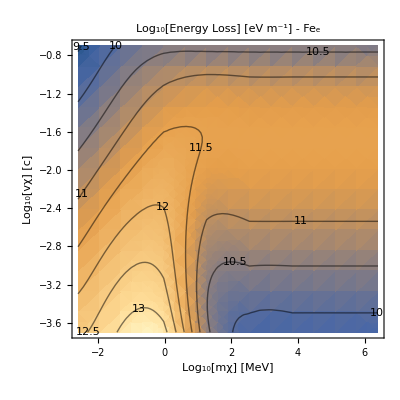

```mathematica
EnergyLoss`PlotEL[FeELOutputDictSIEnhanced,"Fe_e"]
```

```mathematica
Log10[("vF")/("c")/.FeELOutputDictSIEnhanced[["fitparams"]]]
```

{-2.25085,-2.16217,-2.04363,-1.7555,-1.05023,-0.388879}

```mathematica
Log10[("ℏ""ωp")/("JpereV")/.FeELOutputDictSIEnhanced[["fitparams"]]]
```

{1.07836,1.21138,1.38919,1.82139,2.87928,3.87131}

So transition happens around the plasmon energy - weight no it doesn’t this is eV

```mathematica
Log10[("ℏ""ωp")/("JpereV")/.FeELOutputDictSIEnhanced[["fitparams"]]]
```

#### Run SiO2

```mathematica
SiO2ELOutputDictSIEnhanced = EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,SiO2Totalparams,True,"SiO2ELOutputDictSIEnhanced"]
```

1 of 32

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000351525 
Prefactor:	2.08918×10^15
dEdr:	7.344×10^11

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.000127807 and 5.06339×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000127807 
Prefactor:	2.77438×10^15
dEdr:	3.54584×10^11

dEdr total: 1.08898×10^12

2 of 32

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.00354939 and 0.000143586 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00354939 
Prefactor:	2.08918×10^13
dEdr:	7.41531×10^10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.00126344 and 0.0000496077 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00126344 
Prefactor:	2.77438×10^13
dEdr:	3.50525×10^10

dEdr total: 1.09206×10^11

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0346403 
Prefactor:	2.08918×10^11
dEdr:	7.23699×10^9

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0132326 
Prefactor:	2.77438×10^11
dEdr:	3.67121×10^9

dEdr total: 1.09082×10^10

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.471856 
Prefactor:	2.08918×10^9
dEdr:	9.85793×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.13956 
Prefactor:	2.77438×10^9
dEdr:	3.87191×10^8

dEdr total: 1.37298×10^9

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.00159771 
Prefactor:	2.08918×10^15
dEdr:	3.33791×10^12

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000612534 
Prefactor:	2.77438×10^15
dEdr:	1.6994×10^12

dEdr total: 5.03731×10^12

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0159658 
Prefactor:	2.08918×10^13
dEdr:	3.33554×10^11

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00612336 
Prefactor:	2.77438×10^13
dEdr:	1.69885×10^11

dEdr total: 5.03439×10^11

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.151787 
Prefactor:	2.08918×10^11
dEdr:	3.17111×10^10

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0595382 
Prefactor:	2.77438×10^11
dEdr:	1.65181×10^10

dEdr total: 4.82292×10^10

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.29341 
Prefactor:	2.08918×10^9
dEdr:	2.70216×10^9

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.615 
Prefactor:	2.77438×10^9
dEdr:	1.70624×10^9

dEdr total: 4.4084×10^9

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00198861 
Prefactor:	2.08918×10^15
dEdr:	4.15457×10^12

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000790046 
Prefactor:	2.77438×10^15
dEdr:	2.19189×10^12

dEdr total: 6.34646×10^12

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0215885 
Prefactor:	2.08918×10^13
dEdr:	4.51023×10^11

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.00814388 
Prefactor:	2.77438×10^13
dEdr:	2.25942×10^11

dEdr total: 6.76965×10^11

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.688779 
Prefactor:	2.08918×10^11
dEdr:	1.43899×10^11

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.231802 
Prefactor:	2.77438×10^11
dEdr:	6.43107×10^10

dEdr total: 2.08209×10^11

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.99067 
Prefactor:	2.08918×10^9
dEdr:	4.15887×10^9

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.02433 
Prefactor:	2.77438×10^9
dEdr:	2.84188×10^9

dEdr total: 7.00076×10^9

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	6.10994×10^-6 
Prefactor:	2.08918×10^15
dEdr:	1.27648×10^10

For mχ = 3.2026×10^-29 , vχ = 60000
L:	2.17143×10^-6 
Prefactor:	2.77438×10^15
dEdr:	6.02436×10^9

dEdr total: 1.87891×10^10

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.0018314 
Prefactor:	2.08918×10^13
dEdr:	3.82612×10^10

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000326412 
Prefactor:	2.77438×10^13
dEdr:	9.05591×10^9

dEdr total: 4.73171×10^10

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.63978 
Prefactor:	2.08918×10^11
dEdr:	1.33662×10^11

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.198339 
Prefactor:	2.77438×10^11
dEdr:	5.50266×10^10

dEdr total: 1.88688×10^11

16 of 32

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.94143 
Prefactor:	2.08918×10^9
dEdr:	4.056×10^9

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.99543 
Prefactor:	2.77438×10^9
dEdr:	2.7617×10^9

dEdr total: 6.8177×10^9

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.82224×10^-6 
Prefactor:	2.08918×10^15
dEdr:	3.80699×10^9

For mχ = 6.18325×10^-28 , vχ = 60000
L:	3.15423×10^-7 
Prefactor:	2.77438×10^15
dEdr:	8.75103×10^8

dEdr total: 4.6821×10^9

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00178935 
Prefactor:	2.08918×10^13
dEdr:	3.73829×10^10

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000308343 
Prefactor:	2.77438×10^13
dEdr:	8.55459×10^9

dEdr total: 4.59375×10^10

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.63967 
Prefactor:	2.08918×10^11
dEdr:	1.33639×10^11

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.198261 
Prefactor:	2.77438×10^11
dEdr:	5.50052×10^10

dEdr total: 1.88644×10^11

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.94132 
Prefactor:	2.08918×10^9
dEdr:	4.05577×10^9

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.995365 
Prefactor:	2.77438×10^9
dEdr:	2.76152×10^9

dEdr total: 6.81729×10^9

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.81074×10^-6 
Prefactor:	2.08918×10^15
dEdr:	3.78297×10^9

For mχ = 1.1938×10^-26 , vχ = 60000
L:	3.10443×10^-7 
Prefactor:	2.77438×10^15
dEdr:	8.61286×10^8

dEdr total: 4.64425×10^9

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00178924 
Prefactor:	2.08918×10^13
dEdr:	3.73805×10^10

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000308294 
Prefactor:	2.77438×10^13
dEdr:	8.55325×10^9

dEdr total: 4.59338×10^10

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.63967 
Prefactor:	2.08918×10^11
dEdr:	1.33639×10^11

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.198261 
Prefactor:	2.77438×10^11
dEdr:	5.50052×10^10

dEdr total: 1.88644×10^11

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.94132 
Prefactor:	2.08918×10^9
dEdr:	4.05577×10^9

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.995365 
Prefactor:	2.77438×10^9
dEdr:	2.76152×10^9

dEdr total: 6.81729×10^9

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.81071×10^-6 
Prefactor:	2.08918×10^15
dEdr:	3.7829×10^9

For mχ = 2.30487×10^-25 , vχ = 60000
L:	3.1043×10^-7 
Prefactor:	2.77438×10^15
dEdr:	8.61249×10^8

dEdr total: 4.64415×10^9

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00178924 
Prefactor:	2.08918×10^13
dEdr:	3.73805×10^10

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000308294 
Prefactor:	2.77438×10^13
dEdr:	8.55325×10^9

dEdr total: 4.59338×10^10

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.63967 
Prefactor:	2.08918×10^11
dEdr:	1.33639×10^11

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.198261 
Prefactor:	2.77438×10^11
dEdr:	5.50052×10^10

dEdr total: 1.88644×10^11

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.94132 
Prefactor:	2.08918×10^9
dEdr:	4.05577×10^9

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.995365 
Prefactor:	2.77438×10^9
dEdr:	2.76152×10^9

dEdr total: 6.81729×10^9

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.81071×10^-6 
Prefactor:	2.08918×10^15
dEdr:	3.7829×10^9

For mχ = 4.45×10^-24 , vχ = 60000
L:	3.1043×10^-7 
Prefactor:	2.77438×10^15
dEdr:	8.61249×10^8

dEdr total: 4.64415×10^9

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00178924 
Prefactor:	2.08918×10^13
dEdr:	3.73805×10^10

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000308294 
Prefactor:	2.77438×10^13
dEdr:	8.55325×10^9

dEdr total: 4.59338×10^10

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.63967 
Prefactor:	2.08918×10^11
dEdr:	1.33639×10^11

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.198261 
Prefactor:	2.77438×10^11
dEdr:	5.50052×10^10

dEdr total: 1.88644×10^11

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.94132 
Prefactor:	2.08918×10^9
dEdr:	4.05577×10^9

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.995365 
Prefactor:	2.77438×10^9
dEdr:	2.76152×10^9

dEdr total: 6.81729×10^9

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{1.08898×10^12,1.09206×10^11,1.09082×10^10,1.37298×10^9},{5.03731×10^12,5.03439×10^11,4.82292×10^10,4.4084×10^9},{6.34646×10^12,6.76965×10^11,2.08209×10^11,7.00076×10^9},{1.87891×10^10,4.73171×10^10,1.88688×10^11,6.8177×10^9},{4.6821×10^9,4.59375×10^10,1.88644×10^11,6.81729×10^9},{4.64425×10^9,4.59338×10^10,1.88644×10^11,6.81729×10^9},{4.64415×10^9,4.59338×10^10,1.88644×10^11,6.81729×10^9},{4.64415×10^9,4.59338×10^10,1.88644×10^11,6.81729×10^9}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→2.0121×10^30,qF→3.90562×10^10,vF→4.52297×10^6,μ→9.3183×10^-18,ωp→8.0075×10^16,α→1/137,χ→0.392567,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2326.72,nI→2.51512×10^29,Z→8,M→9.27329×10^-26,EF→9.3183×10^-18,ωi→8.0075×10^16,νi→6.06034×10^16,Ai→0.0871584,ωedgei→0}},fname→SiO2ELOutputDictSIEnhanced,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{232.583,416.648,410.152,459.871},{9.64217,9.44281,13.4642,76.8216},{9.48677,9.63862,23.4098,219.167},{8.59071,8.70342,18.1558,140.947},{9.9838,9.33565,17.3556,105.398},{8.26658,8.7981,17.9966,106.194},{9.0922,8.82802,18.079,114.071},{8.38272,8.86135,18.7079,103.545}},totalTime→2639.62|>

#### Plot SiO2

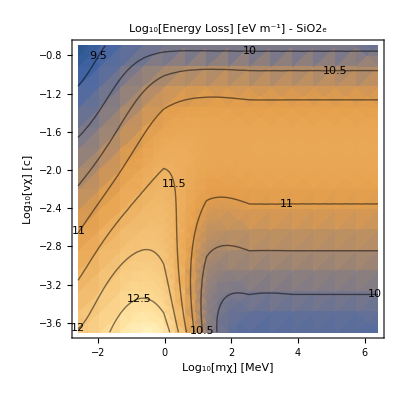

```mathematica
EnergyLoss`PlotEL[SiO2ELOutputDictSIEnhanced,"SiO2_e"]
```

```mathematica
Log10[("vF")/("c")/.SiO2ELOutputDictSIEnhanced[["fitparams"]]]
```

{-2.05304,-1.8217}

#### Run MgO

```mathematica
MgOELOutputDictSIEnhanced = EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,MgOTotalparams,True,"MgOELOutputDictSIEnhanced"]
```

1 of 32

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1987.19}. NIntegrate obtained 0.000677477 and 8.77233×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000677477 
Prefactor:	3.99192×10^13
dEdr:	2.70444×10^10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1983.01}. NIntegrate obtained 0.000417612 and 2.17906×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000417612 
Prefactor:	5.73915×10^14
dEdr:	2.39674×10^11

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.000366232 and 8.02617×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000366232 
Prefactor:	4.00973×10^14
dEdr:	1.46849×10^11

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000133828 
Prefactor:	1.00279×10^16
dEdr:	1.34202×10^12

dEdr total: 1.75558×10^12

2 of 32

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00676784 
Prefactor:	3.99192×10^11
dEdr:	2.70167×10^9

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00428941 
Prefactor:	5.73915×10^12
dEdr:	2.46176×10^10

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00368004 
Prefactor:	4.00973×10^12
dEdr:	1.4756×10^10

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00119429 
Prefactor:	1.00279×10^14
dEdr:	1.19762×10^11

dEdr total: 1.61837×10^11

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0680368 
Prefactor:	3.99192×10^9
dEdr:	2.71598×10^8

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0418825 
Prefactor:	5.73915×10^10
dEdr:	2.4037×10^9

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0368968 
Prefactor:	4.00973×10^10
dEdr:	1.47946×10^9

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.012644 
Prefactor:	1.00279×10^12
dEdr:	1.26793×10^10

dEdr total: 1.68341×10^10

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.942324 
Prefactor:	3.99192×10^7
dEdr:	3.76169×10^7

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.587386 
Prefactor:	5.73915×10^8
dEdr:	3.3711×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.520861 
Prefactor:	4.00973×10^8
dEdr:	2.08851×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.142431 
Prefactor:	1.00279×10^10
dEdr:	1.42828×10^9

dEdr total: 2.01186×10^9

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.00310941 
Prefactor:	3.99192×10^13
dEdr:	1.24125×10^11

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.00190398 
Prefactor:	5.73915×10^14
dEdr:	1.09272×10^12

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.00170066 
Prefactor:	4.00973×10^14
dEdr:	6.81919×10^11

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000605161 
Prefactor:	1.00279×10^16
dEdr:	6.0685×10^12

dEdr total: 7.96727×10^12

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0310574 
Prefactor:	3.99192×10^11
dEdr:	1.23979×10^10

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0190249 
Prefactor:	5.73915×10^12
dEdr:	1.09187×10^11

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0169945 
Prefactor:	4.00973×10^12
dEdr:	6.81434×10^10

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00604949 
Prefactor:	1.00279×10^14
dEdr:	6.06638×10^11

dEdr total: 7.96366×10^11

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.287048 
Prefactor:	3.99192×10^9
dEdr:	1.14587×10^9

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.178594 
Prefactor:	5.73915×10^10
dEdr:	1.02498×10^10

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.160216 
Prefactor:	4.00973×10^10
dEdr:	6.42425×10^9

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0589152 
Prefactor:	1.00279×10^12
dEdr:	5.90797×10^10

dEdr total: 7.68996×10^10

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	2.08821 
Prefactor:	3.99192×10^7
dEdr:	8.33597×10^7

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.44809 
Prefactor:	5.73915×10^8
dEdr:	8.3108×10^8

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.32979 
Prefactor:	4.00973×10^8
dEdr:	5.3321×10^8

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.617751 
Prefactor:	1.00279×10^10
dEdr:	6.19476×10^9

dEdr total: 7.64241×10^9

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00335559 
Prefactor:	3.99192×10^13
dEdr:	1.33952×10^11

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00204764 
Prefactor:	5.73915×10^14
dEdr:	1.17517×10^12

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00182489 
Prefactor:	4.00973×10^14
dEdr:	7.31733×10^11

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000955393 
Prefactor:	1.00279×10^16
dEdr:	9.58059×10^12

dEdr total: 1.16215×10^13

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.039215 
Prefactor:	3.99192×10^11
dEdr:	1.56543×10^10

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0224327 
Prefactor:	5.73915×10^12
dEdr:	1.28745×10^11

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0197807 
Prefactor:	4.00973×10^12
dEdr:	7.93151×10^10

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.00982772 
Prefactor:	1.00279×10^14
dEdr:	9.85515×10^11

dEdr total: 1.20923×10^12

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	1.27045 
Prefactor:	3.99192×10^9
dEdr:	5.07155×10^9

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.819155 
Prefactor:	5.73915×10^10
dEdr:	4.70126×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.735981 
Prefactor:	4.00973×10^10
dEdr:	2.95108×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.235906 
Prefactor:	1.00279×10^12
dEdr:	2.36564×10^11

dEdr total: 3.18159×10^11

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	3.05991 
Prefactor:	3.99192×10^7
dEdr:	1.22149×10^8

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	2.17575 
Prefactor:	5.73915×10^8
dEdr:	1.2487×10^9

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	2.01056 
Prefactor:	4.00973×10^8
dEdr:	8.06181×10^8

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.05774 
Prefactor:	1.00279×10^10
dEdr:	1.06069×10^10

dEdr total: 1.27839×10^10

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	0.0000106813 
Prefactor:	3.99192×10^13
dEdr:	4.26388×10^8

For mχ = 3.2026×10^-29 , vχ = 60000
L:	5.61682×10^-6 
Prefactor:	5.73915×10^14
dEdr:	3.22358×10^9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	4.87482×10^-6 
Prefactor:	4.00973×10^14
dEdr:	1.95467×10^9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	3.08945×10^-6 
Prefactor:	1.00279×10^16
dEdr:	3.09808×10^10

dEdr total: 3.65854×10^10

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00467195 
Prefactor:	3.99192×10^11
dEdr:	1.86501×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00177847 
Prefactor:	5.73915×10^12
dEdr:	1.02069×10^10

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.0014224 
Prefactor:	4.00973×10^12
dEdr:	5.70343×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000533181 
Prefactor:	1.00279×10^14
dEdr:	5.34669×10^10

dEdr total: 7.12423×10^10

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	1.20234 
Prefactor:	3.99192×10^9
dEdr:	4.79965×10^9

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.768872 
Prefactor:	5.73915×10^10
dEdr:	4.41267×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.689255 
Prefactor:	4.00973×10^10
dEdr:	2.76373×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.198977 
Prefactor:	1.00279×10^12
dEdr:	1.99533×10^11

dEdr total: 2.76096×10^11

16 of 32

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	2.99132 
Prefactor:	3.99192×10^7
dEdr:	1.19411×10^8

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	2.12437 
Prefactor:	5.73915×10^8
dEdr:	1.21921×10^9

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.96249 
Prefactor:	4.00973×10^8
dEdr:	7.86906×10^8

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.02666 
Prefactor:	1.00279×10^10
dEdr:	1.02953×10^10

dEdr total: 1.24208×10^10

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	4.5982×10^-6 
Prefactor:	3.99192×10^13
dEdr:	1.83557×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.74719×10^-6 
Prefactor:	5.73915×10^14
dEdr:	1.00274×10^9

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.39524×10^-6 
Prefactor:	4.00973×10^14
dEdr:	5.59453×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	5.24759×10^-7 
Prefactor:	1.00279×10^16
dEdr:	5.26224×10^9

dEdr total: 7.00799×10^9

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00460426 
Prefactor:	3.99192×10^11
dEdr:	1.83798×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00173777 
Prefactor:	5.73915×10^12
dEdr:	9.97335×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00138611 
Prefactor:	4.00973×10^12
dEdr:	5.55793×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000508991 
Prefactor:	1.00279×10^14
dEdr:	5.10412×10^10

dEdr total: 6.84105×10^10

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	1.20219 
Prefactor:	3.99192×10^9
dEdr:	4.79903×10^9

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.768759 
Prefactor:	5.73915×10^10
dEdr:	4.41202×10^10

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.689151 
Prefactor:	4.00973×10^10
dEdr:	2.76331×10^10

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.198892 
Prefactor:	1.00279×10^12
dEdr:	1.99447×10^11

dEdr total: 2.75999×10^11

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	2.99007 
Prefactor:	3.99192×10^7
dEdr:	1.19361×10^8

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	2.12426 
Prefactor:	5.73915×10^8
dEdr:	1.21914×10^9

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.96238 
Prefactor:	4.00973×10^8
dEdr:	7.86862×10^8

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.02659 
Prefactor:	1.00279×10^10
dEdr:	1.02946×10^10

dEdr total: 1.24199×10^10

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	4.58189×10^-6 
Prefactor:	3.99192×10^13
dEdr:	1.82906×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.73682×10^-6 
Prefactor:	5.73915×10^14
dEdr:	9.96787×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.38591×10^-6 
Prefactor:	4.00973×10^14
dEdr:	5.55713×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	5.17875×10^-7 
Prefactor:	1.00279×10^16
dEdr:	5.19321×10^9

dEdr total: 6.92861×10^9

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00460408 
Prefactor:	3.99192×10^11
dEdr:	1.83791×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00173766 
Prefactor:	5.73915×10^12
dEdr:	9.97272×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00138601 
Prefactor:	4.00973×10^12
dEdr:	5.55754×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000508926 
Prefactor:	1.00279×10^14
dEdr:	5.10347×10^10

dEdr total: 6.84029×10^10

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	1.20219 
Prefactor:	3.99192×10^9
dEdr:	4.79903×10^9

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.768758 
Prefactor:	5.73915×10^10
dEdr:	4.41202×10^10

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.68915 
Prefactor:	4.00973×10^10
dEdr:	2.76331×10^10

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.198891 
Prefactor:	1.00279×10^12
dEdr:	1.99446×10^11

dEdr total: 2.75999×10^11

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	2.99114 
Prefactor:	3.99192×10^7
dEdr:	1.19404×10^8

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	2.12426 
Prefactor:	5.73915×10^8
dEdr:	1.21914×10^9

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.96238 
Prefactor:	4.00973×10^8
dEdr:	7.86862×10^8

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.02659 
Prefactor:	1.00279×10^10
dEdr:	1.02946×10^10

dEdr total: 1.242×10^10

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	4.58185×10^-6 
Prefactor:	3.99192×10^13
dEdr:	1.82904×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.73679×10^-6 
Prefactor:	5.73915×10^14
dEdr:	9.96771×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.38588×10^-6 
Prefactor:	4.00973×10^14
dEdr:	5.55703×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	5.17857×10^-7 
Prefactor:	1.00279×10^16
dEdr:	5.19302×10^9

dEdr total: 6.9284×10^9

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00460408 
Prefactor:	3.99192×10^11
dEdr:	1.83791×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00173766 
Prefactor:	5.73915×10^12
dEdr:	9.97272×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00138601 
Prefactor:	4.00973×10^12
dEdr:	5.55754×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000508926 
Prefactor:	1.00279×10^14
dEdr:	5.10347×10^10

dEdr total: 6.84029×10^10

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	1.20219 
Prefactor:	3.99192×10^9
dEdr:	4.79903×10^9

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.768758 
Prefactor:	5.73915×10^10
dEdr:	4.41202×10^10

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.68915 
Prefactor:	4.00973×10^10
dEdr:	2.76331×10^10

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.198891 
Prefactor:	1.00279×10^12
dEdr:	1.99446×10^11

dEdr total: 2.75999×10^11

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	2.99114 
Prefactor:	3.99192×10^7
dEdr:	1.19404×10^8

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	2.12426 
Prefactor:	5.73915×10^8
dEdr:	1.21914×10^9

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.96238 
Prefactor:	4.00973×10^8
dEdr:	7.86863×10^8

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.02659 
Prefactor:	1.00279×10^10
dEdr:	1.02946×10^10

dEdr total: 1.242×10^10

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	4.58185×10^-6 
Prefactor:	3.99192×10^13
dEdr:	1.82904×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.73679×10^-6 
Prefactor:	5.73915×10^14
dEdr:	9.96771×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.38588×10^-6 
Prefactor:	4.00973×10^14
dEdr:	5.55703×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	5.17857×10^-7 
Prefactor:	1.00279×10^16
dEdr:	5.19302×10^9

dEdr total: 6.9284×10^9

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00460408 
Prefactor:	3.99192×10^11
dEdr:	1.83791×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00173766 
Prefactor:	5.73915×10^12
dEdr:	9.97272×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00138601 
Prefactor:	4.00973×10^12
dEdr:	5.55754×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000508926 
Prefactor:	1.00279×10^14
dEdr:	5.10347×10^10

dEdr total: 6.84029×10^10

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	1.20219 
Prefactor:	3.99192×10^9
dEdr:	4.79903×10^9

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.768758 
Prefactor:	5.73915×10^10
dEdr:	4.41202×10^10

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.68915 
Prefactor:	4.00973×10^10
dEdr:	2.76331×10^10

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.198891 
Prefactor:	1.00279×10^12
dEdr:	1.99446×10^11

dEdr total: 2.75999×10^11

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	2.99113 
Prefactor:	3.99192×10^7
dEdr:	1.19404×10^8

For mχ = 4.45×10^-24 , vχ = 60000000
L:	2.12426 
Prefactor:	5.73915×10^8
dEdr:	1.21914×10^9

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.96238 
Prefactor:	4.00973×10^8
dEdr:	7.86862×10^8

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.02659 
Prefactor:	1.00279×10^10
dEdr:	1.02946×10^10

dEdr total: 1.242×10^10

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{1.75558×10^12,1.61837×10^11,1.68341×10^10,2.01186×10^9},{7.96727×10^12,7.96366×10^11,7.68996×10^10,7.64241×10^9},{1.16215×10^13,1.20923×10^12,3.18159×10^11,1.27839×10^10},{3.65854×10^10,7.12423×10^10,2.76096×10^11,1.24208×10^10},{7.00799×10^9,6.84105×10^10,2.75999×10^11,1.24199×10^10},{6.92861×10^9,6.84029×10^10,2.75999×10^11,1.242×10^10},{6.9284×10^9,6.84029×10^10,2.75999×10^11,1.242×10^10},{6.9284×10^9,6.84029×10^10,2.75999×10^11,1.242×10^10}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.50385×10^29,qF→1.64516×10^10,vF→1.90521×10^6,μ→1.65338×10^-18,ωp→2.18914×10^16,α→1/137,χ→0.604859,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→412.839,nI→1.87981×10^28,Z→8,M→9.27329×10^-26,EF→1.65338×10^-18,ωi→2.18914×10^16,νi→4.25006×10^15,Ai→0.039834,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.58115×10^29,qF→2.19692×10^10,vF→2.54418×10^6,μ→2.94839×10^-18,ωp→3.37819×10^16,α→1/137,χ→0.523421,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→736.197,nI→4.47644×10^28,Z→8,M→9.27329×10^-26,EF→2.94839×10^-18,ωi→3.37819×10^16,νi→5.06751×10^15,Ai→0.180092,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.37351×10^29,qF→2.34828×10^10,vF→2.71947×10^6,μ→3.36866×10^-18,ωp→3.73325×10^16,α→1/137,χ→0.506271,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→841.135,nI→5.46689×10^28,Z→8,M→9.27329×10^-26,EF→3.36866×10^-18,ωi→3.73325×10^16,νi→5.23006×10^15,Ai→0.0963866,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.61838×10^30,qF→3.63218×10^10,vF→4.20631×10^6,μ→8.05919×10^-18,ωp→7.18146×10^16,α→1/137,χ→0.407075,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2012.33,nI→2.02298×10^29,Z→8,M→9.27329×10^-26,EF→8.05919×10^-18,ωi→7.18146×10^16,νi→1.12397×10^17,Ai→0.421157,ωedgei→0}},fname→MgOELOutputDictSIEnhanced,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{588.296,782.035,742.519,757.293},{17.8798,22.1166,39.1479,208.248},{16.1366,22.6265,77.9181,356.18},{16.7538,25.2747,63.793,353.342},{20.3762,24.0986,62.6651,300.114},{17.7446,22.5605,62.1735,297.124},{17.4071,24.3837,62.9895,308.185},{16.5445,23.0175,59.4409,294.846}},totalTime→5703.23|>

#### Plot MgO

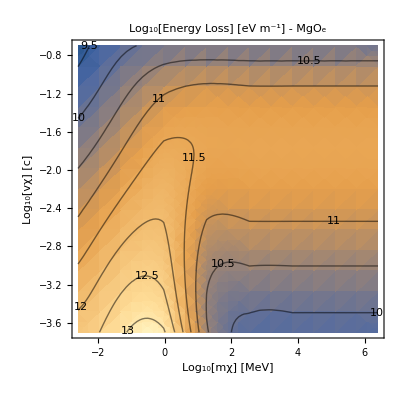

```mathematica
EnergyLoss`PlotEL[MgOELOutputDictSIEnhanced,"MgO_e"]
```

```mathematica
Log10[("vF")/("c")/.MgOELOutputDictSIEnhanced[["fitparams"]]]
```

{-2.19718,-2.07157,-2.04264,-1.85322}